```mathematica
traindata = {8.032467971728272,8.012695941112556,8.032182275376337,8.010080278551076,7.9975097398530215,7.985221699489553,7.994936200963193,7.99537560371486,7.992946072761433,7.9713515780266,7.948684129497854,7.944185321712874,7.921426200162531,7.9326595788238485,7.895465553610329,7.879790713716036,7.8674638773183645,7.842277293197813,7.872278721785054,7.837568924914823,7.814437849763587,7.817444664065407,7.797162081742523,7.784671373691543,7.7370996776391685,7.723056837593496,7.69666150701769,7.671241116812825,7.607982793029604,7.607507969319515,7.5487978979854695,7.525227498499667,7.476117792568545,7.473547362665268,7.416249151817433,7.413465394603588,7.383403843984031,7.381957350324267,7.31810851669959,7.2818068690276245,7.247104549651715,7.257566809555159,7.202744965616197,7.199465438077721,7.1125987527199825,7.143730475955545,7.0982891209120735,7.030202452250596,7.018269121715253,7.063161647655058,6.9707120811351375,6.97879451165019,6.990447914063074,6.946481716712989,6.941904034116471,6.8889781318473355,6.825205661505725,6.833074205406176,6.764664093456284,6.691061740333539,6.723066867057714,6.710240589034893,6.705605257219974,6.678996584381269,6.651611894091222,6.655928683074982,6.575520397427965,6.5634811823279895,6.495220925259617,6.583224104268381,6.55395793007928,6.470036266267998,6.402224736516002,6.499809297696329,6.382039068099187,6.444291380514213,6.406684661747509,6.426132734756947,6.395714972243398,6.286394509586728,6.263139356190752,6.291673070291022,6.3013154150809045,6.1666189649507706,6.1673984006350135,6.181748249967487,6.249363599669745}
```

{8.03247,8.0127,8.03218,8.01008,7.99751,7.98522,7.99494,7.99538,7.99295,7.97135,7.94868,7.94419,7.92143,7.93266,7.89547,7.87979,7.86746,7.84228,7.87228,7.83757,7.81444,7.81744,7.79716,7.78467,7.7371,7.72306,7.69666,7.67124,7.60798,7.60751,7.5488,7.52523,7.47612,7.47355,7.41625,7.41347,7.3834,7.38196,7.31811,7.28181,7.2471,7.25757,7.20274,7.19947,7.1126,7.14373,7.09829,7.0302,7.01827,7.06316,6.97071,6.97879,6.99045,6.94648,6.9419,6.88898,6.82521,6.83307,6.76466,6.69106,6.72307,6.71024,6.70561,6.679,6.65161,6.65593,6.57552,6.56348,6.49522,6.58322,6.55396,6.47004,6.40222,6.49981,6.38204,6.44429,6.40668,6.42613,6.39571,6.28639,6.26314,6.29167,6.30132,6.16662,6.1674,6.18175,6.24936}

```mathematica
testdata = {8.03097152709961,8.012226104736328,7.998507022857666,7.980460166931152,7.968465805053711,7.94732666015625,7.933853626251221,7.912616729736328,7.884011745452881,7.862393379211426,7.835366249084473,7.791564464569092,7.741366863250732,7.6947503089904785,7.655344486236572,7.597153186798096,7.53939151763916,7.483174800872803,7.433498859405518,7.384383201599121,7.327765464782715,7.27947998046875,7.22280216217041,7.179507255554199,7.140140056610107,7.080393314361572,7.067407131195068,7.006697654724121,6.977978706359863,6.930964946746826,6.8766703605651855,6.8495774269104,6.803221702575684,6.831997871398926,6.725269794464111,6.687633991241455,6.647367477416992,6.584807395935059,6.615235805511475,6.540441989898682,6.515263557434082,6.458735942840576,6.490025520324707,6.403131008148193,6.396971225738525}
```

{8.03097,8.01223,7.99851,7.98046,7.96847,7.94733,7.93385,7.91262,7.88401,7.86239,7.83537,7.79156,7.74137,7.69475,7.65534,7.59715,7.53939,7.48317,7.4335,7.38438,7.32777,7.27948,7.2228,7.17951,7.14014,7.08039,7.06741,7.0067,6.97798,6.93096,6.87667,6.84958,6.80322,6.832,6.72527,6.68763,6.64737,6.58481,6.61524,6.54044,6.51526,6.45874,6.49003,6.40313,6.39697}

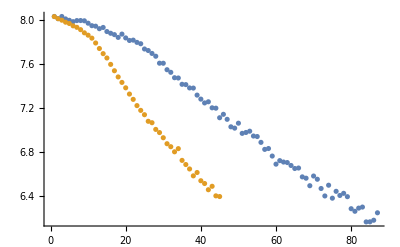

```mathematica
ListPlot[{traindata, testdata}]
```

```mathematica
newtraindata = {15.797724286773471,15.772907686740512,15.713722049493512,15.670204154705816,15.662741315725173,15.604115915169134,15.56101605850324,15.52061140598362,13.68996626153961,11.206129324268323,10.26916850310357,10.131534079148977,10.697940504799153,10.281852617147285,10.009899204983157,10.516510525181122,10.339452151157236,10.22033636337575,10.20604526080824,9.762030815367012,10.595417697332369,9.89678084901901,10.164571393068192,9.604096112450689,9.719901534360838,9.068580234093274,8.720886221802855,9.813469733065544,9.290319035214496,9.449340442687463,9.043449317248523,9.05681046740387,9.650281800560759,9.401863885808035,8.875522721735454,8.506425942359781,8.064627206029689,8.630454002494638,8.880952869730669,7.582739481967769,8.473985507085827,8.147406858986976,7.774066054058556,8.275566545252977,8.243178018057767,8.098331279084004,8.302575966385456,8.322309170348507,8.382330395275137,8.05822303811884,8.541254289889181,8.125675851754457,8.210997253364003,7.502814271885018,7.8346918124123555,7.665079022167103,7.724007279564813,7.932181675885913,7.725814663784515,7.9718988008537375,7.899587172963041,7.88798709780635,8.113499459271454,6.8323514493073025,7.389819239667715,7.463615196330308,7.057888681313024,7.405546919639315,7.338337113141273,7.576261206195289,7.814103564151585,7.316380089969788,7.76892768717432,7.708501279756832,7.310571305805407,7.360658019460673,7.805228402999943,6.645583167202992,6.578568603983529,7.101490838171794,7.561143547235364,6.752507301679658,6.996630056525939,7.41200319363641,6.923693752256401,7.060914560782619,6.8546600058480704,6.821167046742105,7.564121479822094,8.031889413499794,6.8725382889328115,7.60359786811915,6.912442067302186,7.0752074687195,7.154318432330296,7.364488589216669,6.918179237210261,6.895023529673771,6.64935742530227,6.663499807431492,7.069199651004742,7.198289168015643,6.910490807659253,7.525152905194225,6.620764117280314,7.724939485013147,7.045974828083152,7.3671643876983435,7.128126586895828,6.671364572889311,7.268982150934204,7.493074430590269,7.296977259355125,6.701918445220899,6.7105825117245885,6.752229830900709,6.524584965466363,6.980631629361133,6.372375682517343,6.353467924474713,6.577827018630177,6.600202471799618,7.354922237973211,6.523092496230388,7.146771083789345,6.645041886844075,7.134815168611872,6.548310625957229,6.6726492712177246,6.397651101445489,6.822873628470676,6.878970263750131,6.473229155870018,6.547327102305491,6.027539899982031,6.35301828573834,6.836198197821793,6.683000052704366,7.008598071974986,5.961050584635881,6.709360848901639,6.435498721123219,6.069547831055783,6.157481424591354,6.303506594748905,5.240614726890337,5.589576506832741,5.902245805273229,6.353199914500469,5.777992247995092,5.867589106499668,6.495918057320466,7.032739310145946,6.01357318721483,6.464636640641624,6.391658514598347,6.794082655763452,6.128779971661987,6.533706147104663,5.576173156638325,6.8666202646642125,6.030817970629918,5.930057450816288,5.9589887936022725,5.408034602792489,5.484706955460768,6.203434817422575,6.873354036693228,5.816367518014485,5.719448879525625,6.360498173170633,6.453866538406349,5.87998779807852,6.240644525480039,6.021497551895237,6.080561647014337,5.6697867079660025,5.933973789981106,6.124248076461608,6.0064439209805185,6.208030434547056,5.979841419911554,5.857292825139458,6.1776340343437415,5.7025565294060945,5.792207411803332,6.024348491997444,6.100436685912049,5.806954754048217,5.423022690720102,5.7771981603813405,6.060416333880363,6.061408510579906,5.6160729248032055,6.400039702985419,5.6047068698527776,6.132106139934964,6.207679194976242,6.416963183338863,6.342986538837181,5.953965937483011,7.64815888495718,6.65571873659677,6.467706626495369,6.8249863814736615,6.027199984941347,5.904672864034725,5.846502073283918,6.198729513330744,5.99548670992112,5.955275274886856,6.681747707670339,6.72018966337661,6.625127901829431,6.299906913178541,6.31396355180338,7.091740593154208,6.873746741015276,7.246732149783947,8.833649300103897,8.328105945708064,7.402202544746163,8.268054568825274,6.647282365426735,8.240081879001405,8.443631899850253,8.542284132846227,7.840484263892497,7.222078598215096,7.4865884338520665,7.859372673385789,7.232948969055673,6.488082839129395,6.633758820356491,6.701434290663498,7.047496005157045,6.16920135122207,6.81910541623465,8.119583725107487,7.6586433888972225,7.357932973433631,6.870532737453196,7.42668778398458,7.882520748636173,8.657789406342872,7.483380251241203,7.672914568561711,6.524640951970343,7.849108783938597,7.913044309136407,7.527135883995424,7.180911521912422,6.989704268366025,9.06304754809151,8.771028217024709,6.850856512865678,7.292890766612224,7.311336918952065,7.234533279275166,7.914118532992319,7.372130906635745,8.226817048533196,8.478885987646493,7.155699675653755,6.947688560593789,7.099989364683138,7.1057190120105735,6.32632110072132,7.295505065759196,7.563044207323561,8.601150956185586,7.594931938907289,6.647446644813024,7.845836782910982,7.995980223000929,7.554133586676854,7.207422861929282,6.977370374670625,7.191092794917641,7.365875445302727,7.5949529236348265,6.915682909719273,7.1327591361679366,7.054351584926791,9.456708966656453,8.928731633679497,7.328865204704909,7.08803977266929,6.401432428113396,6.278091388411449,6.637386835825993,6.656379993794628,6.384068056489543,6.9875224083797995,6.483310691283637,6.260455840645286,6.369735038680676,6.247464361742747,6.913138691110289,5.720055712973264,6.5036569718370085,6.404941534848751,5.6893311890425595,5.834151913808892,5.8769321051099395,5.417393268007921,6.45314202981652,5.800287654923808,5.998778720867904,5.767959538923845,6.040443258287974,5.526958709902198,5.935264787748013,5.98537099695422,6.469343488704814,6.115682329354046,5.8567681206738404,6.276110018336702,6.154964724545009,6.399546646157387,6.346610790843825,6.435528363570048,6.632729007808468,7.193939295160928,6.189315853805436,5.995202090689641,6.847943285605567,6.3418611956082955,5.762260088639801,6.405430923500469,6.457086651292432,6.118588716395404,6.386813383154285,7.031196181933605,6.53106469517471,6.4207655066374665,6.422873292731967,6.254583926778229,6.925917898661024,6.692615452300321,6.617856516028578,5.763993697187501,6.811368037421618,5.991944613287749,6.8190146513760554,6.07799208819275,6.621759224153886,6.330600960189597,6.412314917352023,5.852455489158209,6.851482370162148,6.068222389042119,5.581663291006184,5.743658868552759,6.080066458095324,5.427145393316606,5.393765272937326,5.6758749099953585,6.195342211312639,5.951248552136361,6.249882716309641,5.764009223906836,5.8876305185357065,6.759437854621574,5.71838523388908,6.347550562531109,6.066364028903304,6.604337536222243,6.36836512806933,6.700509567221296,6.049046896189932,7.465128597755005,6.795476560456173,7.257069390735694,7.767724578154852,7.66656250727567,7.2837685149018725,6.89053825562278,7.040295299710015,7.633896667301502,7.031511703683625,6.615640248162066,6.760125171171751,6.476611839055119,6.207781178527675,7.21714772328352,5.65804423465255,6.265795046781764,6.0337379413202985,6.620106678139024,6.443147465384357,6.306454655795932,6.372105409444173,6.9058037825852265,6.197507037419317,5.98913568885086,6.1041758280368095,6.720424201461863,6.80857560675834,6.643396898689052,7.029733925783575,6.791349524294813,6.740547348293454,7.042213177508554,7.124185274153859,5.9886957804804775,6.9225095628372175,6.358518302382098,6.31617655507566,6.444427649612072,7.014992203999375,6.988040744135981,7.234284117473176,6.950017200327503,7.09724872957577,6.851935923482625,6.309712580738973,6.694840641656478,6.945201622481535,6.476948111118477,6.790671751247743,6.657771445191844,7.436328056864129,7.290082115053497,7.528287515109704,6.980496521130675,7.458317230843228,6.888139052473864,7.200861241027338}
```

{15.7977,15.7729,15.7137,15.6702,15.6627,15.6041,15.561,15.5206,13.69,11.2061,10.2692,10.1315,10.6979,10.2819,10.0099,10.5165,10.3395,10.2203,10.206,9.76203,10.5954,9.89678,10.1646,9.6041,9.7199,9.06858,8.72089,9.81347,9.29032,9.44934,9.04345,9.05681,9.65028,9.40186,8.87552,8.50643,8.06463,8.63045,8.88095,7.58274,8.47399,8.14741,7.77407,8.27557,8.24318,8.09833,8.30258,8.32231,8.38233,8.05822,8.54125,8.12568,8.211,7.50281,7.83469,7.66508,7.72401,7.93218,7.72581,7.9719,7.89959,7.88799,8.1135,6.83235,7.38982,7.46362,7.05789,7.40555,7.33834,7.57626,7.8141,7.31638,7.76893,7.7085,7.31057,7.36066,7.80523,6.64558,6.57857,7.10149,7.56114,6.75251,6.99663,7.412,6.92369,7.06091,6.85466,6.82117,7.56412,8.03189,6.87254,7.6036,6.91244,7.07521,7.15432,7.36449,6.91818,6.89502,6.64936,6.6635,7.0692,7.19829,6.91049,7.52515,6.62076,7.72494,7.04597,7.36716,7.12813,6.67136,7.26898,7.49307,7.29698,6.70192,6.71058,6.75223,6.52458,6.98063,6.37238,6.35347,6.57783,6.6002,7.35492,6.52309,7.14677,6.64504,7.13482,6.54831,6.67265,6.39765,6.82287,6.87897,6.47323,6.54733,6.02754,6.35302,6.8362,6.683,7.0086,5.96105,6.70936,6.4355,6.06955,6.15748,6.30351,5.24061,5.58958,5.90225,6.3532,5.77799,5.86759,6.49592,7.03274,6.01357,6.46464,6.39166,6.79408,6.12878,6.53371,5.57617,6.86662,6.03082,5.93006,5.95899,5.40803,5.48471,6.20343,6.87335,5.81637,5.71945,6.3605,6.45387,5.87999,6.24064,6.0215,6.08056,5.66979,5.93397,6.12425,6.00644,6.20803,5.97984,5.85729,6.17763,5.70256,5.79221,6.02435,6.10044,5.80695,5.42302,5.7772,6.06042,6.06141,5.61607,6.40004,5.60471,6.13211,6.20768,6.41696,6.34299,5.95397,7.64816,6.65572,6.46771,6.82499,6.0272,5.90467,5.8465,6.19873,5.99549,5.95528,6.68175,6.72019,6.62513,6.29991,6.31396,7.09174,6.87375,7.24673,8.83365,8.32811,7.4022,8.26805,6.64728,8.24008,8.44363,8.54228,7.84048,7.22208,7.48659,7.85937,7.23295,6.48808,6.63376,6.70143,7.0475,6.1692,6.81911,8.11958,7.65864,7.35793,6.87053,7.42669,7.88252,8.65779,7.48338,7.67291,6.52464,7.84911,7.91304,7.52714,7.18091,6.9897,9.06305,8.77103,6.85086,7.29289,7.31134,7.23453,7.91412,7.37213,8.22682,8.47889,7.1557,6.94769,7.09999,7.10572,6.32632,7.29551,7.56304,8.60115,7.59493,6.64745,7.84584,7.99598,7.55413,7.20742,6.97737,7.19109,7.36588,7.59495,6.91568,7.13276,7.05435,9.45671,8.92873,7.32887,7.08804,6.40143,6.27809,6.63739,6.65638,6.38407,6.98752,6.48331,6.26046,6.36974,6.24746,6.91314,5.72006,6.50366,6.40494,5.68933,5.83415,5.87693,5.41739,6.45314,5.80029,5.99878,5.76796,6.04044,5.52696,5.93526,5.98537,6.46934,6.11568,5.85677,6.27611,6.15496,6.39955,6.34661,6.43553,6.63273,7.19394,6.18932,5.9952,6.84794,6.34186,5.76226,6.40543,6.45709,6.11859,6.38681,7.0312,6.53106,6.42077,6.42287,6.25458,6.92592,6.69262,6.61786,5.76399,6.81137,5.99194,6.81901,6.07799,6.62176,6.3306,6.41231,5.85246,6.85148,6.06822,5.58166,5.74366,6.08007,5.42715,5.39377,5.67587,6.19534,5.95125,6.24988,5.76401,5.88763,6.75944,5.71839,6.34755,6.06636,6.60434,6.36837,6.70051,6.04905,7.46513,6.79548,7.25707,7.76772,7.66656,7.28377,6.89054,7.0403,7.6339,7.03151,6.61564,6.76013,6.47661,6.20778,7.21715,5.65804,6.2658,6.03374,6.62011,6.44315,6.30645,6.37211,6.9058,6.19751,5.98914,6.10418,6.72042,6.80858,6.6434,7.02973,6.79135,6.74055,7.04221,7.12419,5.9887,6.92251,6.35852,6.31618,6.44443,7.01499,6.98804,7.23428,6.95002,7.09725,6.85194,6.30971,6.69484,6.9452,6.47695,6.79067,6.65777,7.43633,7.29008,7.52829,6.9805,7.45832,6.88814,7.20086}

```mathematica
newtestdata = {7.90723180770874,7.895229816436768,7.869626522064209,7.856346130371094,7.83223819732666,7.83035135269165,7.8035173416137695,7.79201078414917,7.753549575805664,3.823969602584839,3.5590405464172363,2.9415698051452637,2.65332293510437,2.6726584434509277,2.7279505729675293,2.7214980125427246,2.8793673515319824,2.62461256980896,2.5762248039245605,2.5948758125305176,2.506148099899292,2.384448528289795,2.589895248413086,2.476393938064575,2.590228796005249,2.3494577407836914,2.3800039291381836,2.3505847454071045,2.4722213745117188,2.4386165142059326,2.567484140396118,2.3778233528137207,2.3369688987731934,2.4062535762786865,2.410907745361328,2.185375690460205,2.212731122970581,2.1696786880493164,2.1106436252593994,2.071255922317505,2.1876862049102783,2.0562593936920166,2.1116578578948975,1.9707893133163452,2.2433981895446777,2.1465539932250977,2.008967638015747,2.0859062671661377,1.9211602210998535,1.9874924421310425,2.255586862564087,2.069593667984009,2.002253770828247,2.100736618041992,2.110121250152588,2.0928757190704346,1.9213824272155762,2.1219804286956787,1.9996449947357178,2.0883452892303467,1.8865892887115479,2.0432400703430176,1.9935929775238037,1.9118796586990356,2.0952203273773193,1.9341719150543213,1.9162627458572388,1.9597519636154175,1.9119775295257568,1.8884693384170532,2.0753390789031982,2.029022455215454,1.9034074544906616,1.929573655128479,1.8585139513015747,1.8333402872085571,1.948045015335083,1.8827080726623535,1.9195237159729004,1.8280718326568604,2.0449271202087402,1.9872478246688843,1.7868084907531738,2.0583410263061523,1.9978290796279907,1.8253566026687622,1.7078574895858765,1.8426047563552856,1.9259378910064697,2.0925519466400146,1.9158118963241577,1.8076534271240234,2.0557701587677,2.0706355571746826,1.7638797760009766,1.943113923072815,2.008974075317383,2.014998197555542,2.0398428440093994,1.9121006727218628,1.997568964958191,1.9589192867279053,2.1154041290283203,1.9320787191390991,1.9761931896209717,2.0196666717529297,2.0240700244903564,1.994224190711975,1.8059049844741821,1.992612600326538,1.9465272426605225,1.9718842506408691,1.9174163341522217,1.9484984874725342,1.7674765586853027,2.0017731189727783,1.9330247640609741,1.9706263542175293,1.9792779684066772,2.1975207328796387,1.9692320823669434,1.9853074550628662,2.037449359893799,1.8960888385772705,1.8938349485397339,1.9442394971847534,1.8494898080825806,1.7678916454315186,1.9948590993881226,1.6808512210845947,1.8340009450912476,1.7798517942428589,1.8004331588745117,1.7375478744506836,1.8100621700286865,1.6538516283035278,1.8422271013259888,1.6611216068267822,1.5814679861068726,1.4019007682800293,1.2489129304885864,1.4592335224151611,1.2309085130691528,1.3874720335006714,1.2954270839691162,1.4581290483474731,1.4010124206542969,1.3869026899337769,1.4776203632354736,1.274867057800293,1.330405354499817,1.2546260356903076,1.4103684425354004,1.3389592170715332,1.3727192878723145,1.3456727266311646,1.3088592290878296,1.411104679107666,1.4629489183425903,1.389877438545227,1.249766230583191,1.2524187564849854,1.3681418895721436,1.361780047416687,1.4327452182769775,1.355919599533081,1.3641549348831177,1.3693859577178955,1.374098539352417,1.2948566675186157,1.365388035774231,1.2084662914276123,1.2291072607040405,1.2663415670394897,1.3759777545928955,1.164754867553711,1.2474292516708374,1.3263881206512451,1.367565393447876,1.2990953922271729,1.2855943441390991,1.168355941772461,1.4829005002975464,1.3109190464019775,1.3799636363983154,1.480568528175354,1.3562251329421997,1.3594458103179932,1.3450660705566406,1.3484870195388794,1.4798890352249146,1.32183039188385,1.3460127115249634,1.3066203594207764,1.2860431671142578,1.2693465948104858,1.3881198167800903,1.3489222526550293,1.2675092220306396,1.3346132040023804,1.4109249114990234,1.6893012523651123,1.7766469717025757,1.6222667694091797,1.553126335144043,1.8397005796432495,1.766466498374939,1.718881607055664,1.4913362264633179,1.603149175643921,1.6383410692214966,1.712136149406433,2.01322603225708,1.98835027217865,1.9230433702468872,1.9842050075531006,1.9430469274520874,2.605811357498169,2.476080894470215,2.8860816955566406,5.491335391998291,3.6221704483032227,5.343177318572998,2.24556565284729,2.800337076187134,2.8144783973693848,5.495135307312012,3.190403938293457,2.554067850112915,2.94010329246521,2.842367172241211,2.7783150672912598,2.2601189613342285,2.2362451553344727,2.3347251415252686,1.9292066097259521,1.8798644542694092,2.461374521255493,2.490449905395508,5.662751197814941,2.784281015396118,2.66188907623291,3.854604959487915,3.2993719577789307,3.312008857727051,2.9014360904693604,2.6313154697418213,2.1678731441497803,2.6626791954040527,2.9813485145568848,2.4581408500671387,2.8009393215179443,2.605724811553955,5.55780029296875,5.309372901916504,2.8382322788238525,2.345266580581665,2.409827709197998,2.4502415657043457,2.627063751220703,5.673431396484375,3.7040579319000244,2.9315872192382812,2.7054522037506104,2.660317897796631,1.8190429210662842,2.02174973487854,2.20051908493042,1.963488221168518,2.8362910747528076,2.6158287525177,5.742613792419434,2.572859048843384,2.619353771209717,2.5629615783691406,2.5181503295898438,2.6232118606567383,5.773318767547607,3.0964882373809814,2.461820602416992,5.549144744873047,2.5386667251586914,2.470010995864868,2.9488508701324463,2.992711067199707,5.578987121582031,2.8450279235839844,2.4231181144714355,1.9483839273452759,1.9399049282073975,2.1294708251953125,1.897722601890564,1.795798659324646,1.97465980052948,2.324596405029297,2.55684232711792,2.5446183681488037,2.0630433559417725,1.898563027381897,2.076481342315674,1.8420369625091553,1.523457646369934,1.467728853225708,1.5730663537979126,1.5582468509674072,1.5066362619400024,1.3014429807662964,1.3768192529678345,1.389122486114502,1.280815601348877,1.4633922576904297,1.4268985986709595,1.808280348777771,1.439879059791565,1.9779802560806274,2.005316734313965,1.9819940328598022,2.1861565113067627,1.9760862588882446,1.9402014017105103,1.7200603485107422,1.8661611080169678,1.9138813018798828,2.041651964187622,1.9943979978561401,1.8090602159500122,2.072601318359375,2.479003429412842,2.2695529460906982,2.1586496829986572,2.100367546081543,1.9292609691619873,1.9176439046859741,2.5019030570983887,2.444321870803833,1.8136053085327148,1.8160755634307861,2.0310873985290527,2.1392009258270264,2.029599189758301,1.8526614904403687,2.124131202697754,1.9163087606430054,2.2886645793914795,1.9145216941833496,1.975432276725769,1.978338599205017,1.800806999206543,1.881209373474121,1.3277044296264648,1.711840271949768,1.9033304452896118,1.6625319719314575,1.7430195808410645,1.313214659690857,1.2709213495254517,1.4083689451217651,1.406362771987915,1.2876313924789429,1.3706986904144287,1.954298496246338,2.0763471126556396,1.8741912841796875,2.254331350326538,2.04677677154541,1.8622606992721558,2.442983865737915,2.1907947063446045,1.892420768737793,2.0304439067840576,2.41123366355896,2.69079852104187,2.5201432704925537,2.9124083518981934,3.8883001804351807,3.551279306411743,3.138226270675659,3.163303852081299,2.393014669418335,3.2431435585021973,3.0609130859375,2.496119260787964,2.7349956035614014,2.556335926055908,1.8515801429748535,2.081256866455078,2.073467969894409,1.9731556177139282,1.8491545915603638,2.24923038482666,2.186715841293335,2.16011381149292,1.9795000553131104,2.0898690223693848,1.8119242191314697,2.056988477706909,2.81740403175354,2.485074520111084,2.550187587738037,3.0862436294555664,3.186955213546753,3.235489845275879,2.626939535140991,2.82779860496521,2.6589553356170654,2.650083065032959,2.688886880874634,2.495676040649414,2.5605597496032715,2.6908628940582275,2.7225794792175293,2.680832862854004,2.737705945968628,2.9411990642547607,2.8045735359191895,2.528144359588623,2.5442423820495605,2.70759916305542,2.7869679927825928,2.5843467712402344,2.6228957176208496,2.7533905506134033,3.1276817321777344,3.163329601287842,2.9083547592163086,2.629457712173462,3.2494070529937744,3.1502559185028076,3.0638651847839355,3.1574738025665283}
```

{7.90723,7.89523,7.86963,7.85635,7.83224,7.83035,7.80352,7.79201,7.75355,3.82397,3.55904,2.94157,2.65332,2.67266,2.72795,2.7215,2.87937,2.62461,2.57622,2.59488,2.50615,2.38445,2.5899,2.47639,2.59023,2.34946,2.38,2.35058,2.47222,2.43862,2.56748,2.37782,2.33697,2.40625,2.41091,2.18538,2.21273,2.16968,2.11064,2.07126,2.18769,2.05626,2.11166,1.97079,2.2434,2.14655,2.00897,2.08591,1.92116,1.98749,2.25559,2.06959,2.00225,2.10074,2.11012,2.09288,1.92138,2.12198,1.99964,2.08835,1.88659,2.04324,1.99359,1.91188,2.09522,1.93417,1.91626,1.95975,1.91198,1.88847,2.07534,2.02902,1.90341,1.92957,1.85851,1.83334,1.94805,1.88271,1.91952,1.82807,2.04493,1.98725,1.78681,2.05834,1.99783,1.82536,1.70786,1.8426,1.92594,2.09255,1.91581,1.80765,2.05577,2.07064,1.76388,1.94311,2.00897,2.015,2.03984,1.9121,1.99757,1.95892,2.1154,1.93208,1.97619,2.01967,2.02407,1.99422,1.8059,1.99261,1.94653,1.97188,1.91742,1.9485,1.76748,2.00177,1.93302,1.97063,1.97928,2.19752,1.96923,1.98531,2.03745,1.89609,1.89383,1.94424,1.84949,1.76789,1.99486,1.68085,1.834,1.77985,1.80043,1.73755,1.81006,1.65385,1.84223,1.66112,1.58147,1.4019,1.24891,1.45923,1.23091,1.38747,1.29543,1.45813,1.40101,1.3869,1.47762,1.27487,1.33041,1.25463,1.41037,1.33896,1.37272,1.34567,1.30886,1.4111,1.46295,1.38988,1.24977,1.25242,1.36814,1.36178,1.43275,1.35592,1.36415,1.36939,1.3741,1.29486,1.36539,1.20847,1.22911,1.26634,1.37598,1.16475,1.24743,1.32639,1.36757,1.2991,1.28559,1.16836,1.4829,1.31092,1.37996,1.48057,1.35623,1.35945,1.34507,1.34849,1.47989,1.32183,1.34601,1.30662,1.28604,1.26935,1.38812,1.34892,1.26751,1.33461,1.41092,1.6893,1.77665,1.62227,1.55313,1.8397,1.76647,1.71888,1.49134,1.60315,1.63834,1.71214,2.01323,1.98835,1.92304,1.98421,1.94305,2.60581,2.47608,2.88608,5.49134,3.62217,5.34318,2.24557,2.80034,2.81448,5.49514,3.1904,2.55407,2.9401,2.84237,2.77832,2.26012,2.23625,2.33473,1.92921,1.87986,2.46137,2.49045,5.66275,2.78428,2.66189,3.8546,3.29937,3.31201,2.90144,2.63132,2.16787,2.66268,2.98135,2.45814,2.80094,2.60572,5.5578,5.30937,2.83823,2.34527,2.40983,2.45024,2.62706,5.67343,3.70406,2.93159,2.70545,2.66032,1.81904,2.02175,2.20052,1.96349,2.83629,2.61583,5.74261,2.57286,2.61935,2.56296,2.51815,2.62321,5.77332,3.09649,2.46182,5.54914,2.53867,2.47001,2.94885,2.99271,5.57899,2.84503,2.42312,1.94838,1.9399,2.12947,1.89772,1.7958,1.97466,2.3246,2.55684,2.54462,2.06304,1.89856,2.07648,1.84204,1.52346,1.46773,1.57307,1.55825,1.50664,1.30144,1.37682,1.38912,1.28082,1.46339,1.4269,1.80828,1.43988,1.97798,2.00532,1.98199,2.18616,1.97609,1.9402,1.72006,1.86616,1.91388,2.04165,1.9944,1.80906,2.0726,2.479,2.26955,2.15865,2.10037,1.92926,1.91764,2.5019,2.44432,1.81361,1.81608,2.03109,2.1392,2.0296,1.85266,2.12413,1.91631,2.28866,1.91452,1.97543,1.97834,1.80081,1.88121,1.3277,1.71184,1.90333,1.66253,1.74302,1.31321,1.27092,1.40837,1.40636,1.28763,1.3707,1.9543,2.07635,1.87419,2.25433,2.04678,1.86226,2.44298,2.19079,1.89242,2.03044,2.41123,2.6908,2.52014,2.91241,3.8883,3.55128,3.13823,3.1633,2.39301,3.24314,3.06091,2.49612,2.735,2.55634,1.85158,2.08126,2.07347,1.97316,1.84915,2.24923,2.18672,2.16011,1.9795,2.08987,1.81192,2.05699,2.8174,2.48507,2.55019,3.08624,3.18696,3.23549,2.62694,2.8278,2.65896,2.65008,2.68889,2.49568,2.56056,2.69086,2.72258,2.68083,2.73771,2.9412,2.80457,2.52814,2.54424,2.7076,2.78697,2.58435,2.6229,2.75339,3.12768,3.16333,2.90835,2.62946,3.24941,3.15026,3.06387,3.15747}

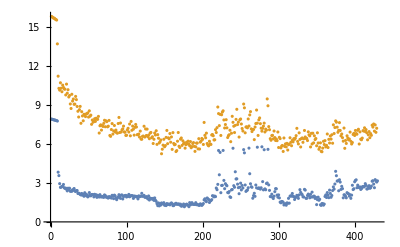

```mathematica
ListPlot[{newtestdata, newtraindata}]
```

```mathematica
finaltestdata = {7.910699367523193,7.90363073348999,7.887001037597656,7.871028900146484,7.858418941497803,7.848133563995361,7.819947242736816,7.8024163246154785,7.777926445007324,7.737869739532471,7.697196960449219,7.653768062591553,7.574106216430664,7.514235019683838,7.4651408195495605,7.385733604431152,7.2984938621521,7.2105584144592285,7.11196756362915,7.083012580871582,6.9600830078125,6.906580448150635,6.903549671173096,6.81752872467041,6.779626846313477,6.782930850982666,6.73499059677124,6.694859504699707,6.693630218505859,6.574243068695068,6.6133713722229,6.539858818054199,6.479861259460449,6.488808631896973,6.515314102172852,6.397181987762451,6.409493446350098,6.2750678062438965,6.348653316497803,6.2047319412231445,6.302140235900879,6.296738147735596,6.260707855224609,6.247731685638428,6.179149627685547,6.142852783203125,6.129787921905518,6.144811153411865,6.068231582641602,6.09036922454834,6.096072196960449,6.0524797439575195,6.085418701171875,6.008403301239014,5.944636821746826,5.995151996612549,5.953817844390869,5.850558280944824,5.954148292541504,5.92173957824707,5.884189128875732,5.9073166847229,5.841726779937744,5.885365009307861,5.881025314331055,5.7795634269714355,5.887636661529541,5.876060485839844,5.812865257263184,5.8275346755981445,5.85446834564209,5.783321380615234,5.780030250549316,5.763962268829346,5.783783912658691,5.8271164894104,5.727029323577881,5.692163467407227,5.657305717468262,5.729042053222656,5.676791191101074,5.721571445465088,5.696800231933594,5.73482084274292,5.7215189933776855,5.69016695022583,5.638990879058838,5.6909661293029785,5.63847541809082,5.768232345581055,5.755088806152344,5.650881767272949,5.579380512237549,5.634119510650635,5.639692306518555,5.667540550231934,5.599459171295166,5.580852031707764,5.544848442077637,5.624685764312744,5.6100921630859375,5.74699068069458,5.566368103027344,5.65427303314209,5.609918594360352,5.531587600708008,5.485659599304199,5.5710954666137695,5.713861465454102,5.549519062042236,5.649227142333984,5.621975421905518,5.648123741149902,5.7089433670043945,5.754486083984375,5.751955509185791,5.586075782775879,5.771380424499512,5.574223518371582,5.596432209014893,5.7793450355529785,5.548593044281006,5.742367267608643,5.55598783493042,5.667507648468018,5.584202289581299,5.614320755004883,5.490703105926514,5.583309650421143,5.557695388793945,5.612287998199463,5.64072847366333,5.633678436279297,5.52289342880249,5.704041004180908,5.654168605804443,5.702066898345947,5.702549457550049}
```

{7.9107,7.90363,7.887,7.87103,7.85842,7.84813,7.81995,7.80242,7.77793,7.73787,7.6972,7.65377,7.57411,7.51424,7.46514,7.38573,7.29849,7.21056,7.11197,7.08301,6.96008,6.90658,6.90355,6.81753,6.77963,6.78293,6.73499,6.69486,6.69363,6.57424,6.61337,6.53986,6.47986,6.48881,6.51531,6.39718,6.40949,6.27507,6.34865,6.20473,6.30214,6.29674,6.26071,6.24773,6.17915,6.14285,6.12979,6.14481,6.06823,6.09037,6.09607,6.05248,6.08542,6.0084,5.94464,5.99515,5.95382,5.85056,5.95415,5.92174,5.88419,5.90732,5.84173,5.88537,5.88103,5.77956,5.88764,5.87606,5.81287,5.82753,5.85447,5.78332,5.78003,5.76396,5.78378,5.82712,5.72703,5.69216,5.65731,5.72904,5.67679,5.72157,5.6968,5.73482,5.72152,5.69017,5.63899,5.69097,5.63848,5.76823,5.75509,5.65088,5.57938,5.63412,5.63969,5.66754,5.59946,5.58085,5.54485,5.62469,5.61009,5.74699,5.56637,5.65427,5.60992,5.53159,5.48566,5.5711,5.71386,5.54952,5.64923,5.62198,5.64812,5.70894,5.75449,5.75196,5.58608,5.77138,5.57422,5.59643,5.77935,5.54859,5.74237,5.55599,5.66751,5.5842,5.61432,5.4907,5.58331,5.5577,5.61229,5.64073,5.63368,5.52289,5.70404,5.65417,5.70207,5.70255}

```mathematica
finaltraindata = {7.913536111017263,7.890502167858817,7.8852105808365165,7.870438761645525,7.849514780575541,7.833648968557529,7.816967850896982,7.763785033920183,7.736249346743948,7.690238534754377,7.640804264231433,7.566598161443743,7.505300711808913,7.433633073995902,7.3997690047904605,7.244941360336902,7.175969266239683,7.073252692913203,7.041792059058874,6.884160525795536,6.828749625776665,6.839263307591725,6.734705291335695,6.707986828881712,6.588751725147632,6.547386124697865,6.490382113576549,6.453050387467727,6.424965489319903,6.380693108326929,6.325092796784855,6.29013178195404,6.347765439364945,6.223698422553709,6.131155754254704,6.186880126624125,6.183095673420309,6.083157180386487,6.0858010111312035,6.115015445012485,5.912333175766174,6.115465409728784,5.9296770358252715,5.947878919529273,5.903771815277996,5.900418749154523,5.8646063270059345,5.871833146399041,5.733118875168892,5.760308215385798,5.7395255625363095,5.802274376471149,5.79361020283788,5.716913212269635,5.711624015591728,5.6965953055881595,5.604997946977164,5.579805984589365,5.568756266946577,5.642698804613491,5.561396480955946,5.431387797228918,5.6233278182032675,5.392726191618699,5.536577115346263,5.524112336780088,5.385699153093785,5.501995847180533,5.446123175526708,5.49196161508421,5.255937675524983,5.449967407850436,5.420267491505739,5.416851186545346,5.303818289960638,5.273881496066389,5.234364859602465,5.234211403115626,5.218603788383181,5.301568076648283,5.340061258152023,5.42849726195605,5.260704376651169,5.140063369748158,5.15409057988863,5.249188568409275,5.339425178388168,5.351596485067358,5.170155691823286,5.199935033201719,5.180218981056026,5.196138744231273,5.1641490041658145,5.201670965739389,5.189387095379365,5.245424679437349,5.251412075391996,5.092057384215375,5.192136073806365,5.095557770580957,5.11817178786871,5.198440046301634,5.190835647263401,5.127762964760293,5.136054798783927,5.171831152342089,5.123422820796508,5.072710768362945,5.147228120088836,4.888125178837197,5.025556004516461,5.187518831135629,5.1239864278324685,5.0655698406817535,5.092768569552038,5.16787837369738,5.021129831419609,5.186409444442623,5.124823107777533,5.146763859062788,5.088052239027326,5.006789498057953,5.013763156402278,5.0224356202389195,5.00086535320014,5.055345216385677,5.025143831342203,4.985453321693008,5.010221165302142,5.062266266519612,4.908844182009442,5.033502847461242,5.159269884899821,5.155582489597191,5.091931567395961,4.967916438958853}
```

{7.91354,7.8905,7.88521,7.87044,7.84951,7.83365,7.81697,7.76379,7.73625,7.69024,7.6408,7.5666,7.5053,7.43363,7.39977,7.24494,7.17597,7.07325,7.04179,6.88416,6.82875,6.83926,6.73471,6.70799,6.58875,6.54739,6.49038,6.45305,6.42497,6.38069,6.32509,6.29013,6.34777,6.2237,6.13116,6.18688,6.1831,6.08316,6.0858,6.11502,5.91233,6.11547,5.92968,5.94788,5.90377,5.90042,5.86461,5.87183,5.73312,5.76031,5.73953,5.80227,5.79361,5.71691,5.71162,5.6966,5.605,5.57981,5.56876,5.6427,5.5614,5.43139,5.62333,5.39273,5.53658,5.52411,5.3857,5.502,5.44612,5.49196,5.25594,5.44997,5.42027,5.41685,5.30382,5.27388,5.23436,5.23421,5.2186,5.30157,5.34006,5.4285,5.2607,5.14006,5.15409,5.24919,5.33943,5.3516,5.17016,5.19994,5.18022,5.19614,5.16415,5.20167,5.18939,5.24542,5.25141,5.09206,5.19214,5.09556,5.11817,5.19844,5.19084,5.12776,5.13605,5.17183,5.12342,5.07271,5.14723,4.88813,5.02556,5.18752,5.12399,5.06557,5.09277,5.16788,5.02113,5.18641,5.12482,5.14676,5.08805,5.00679,5.01376,5.02244,5.00087,5.05535,5.02514,4.98545,5.01022,5.06227,4.90884,5.0335,5.15927,5.15558,5.09193,4.96792}

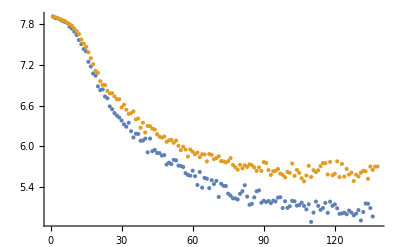

```mathematica
ListPlot[{finaltraindata, finaltestdata}]
```

```mathematica
test10data = {7.923801898956299,6.317034721374512,3.9198663234710693,2.8861889839172363,3.00573992729187,3.3135159015655518,3.3149044513702393,4.042707920074463,4.017055988311768,3.011552572250366,3.304917335510254,3.1623620986938477,3.3204421997070312,3.362441062927246,3.2376644611358643,3.2574257850646973,3.183940887451172,2.931972026824951,2.8033528327941895,2.693502426147461,3.053736925125122,2.8018226623535156,2.720207452774048,2.7636876106262207,2.86049747467041,2.5899312496185303,2.5211808681488037,2.4415194988250732,2.5157063007354736,2.3524081707000732,2.308061361312866,2.403407335281372,2.2319040298461914,2.231987953186035}
```

{7.9238,6.31703,3.91987,2.88619,3.00574,3.31352,3.3149,4.04271,4.01706,3.01155,3.30492,3.16236,3.32044,3.36244,3.23766,3.25743,3.18394,2.93197,2.80335,2.6935,3.05374,2.80182,2.72021,2.76369,2.8605,2.58993,2.52118,2.44152,2.51571,2.35241,2.30806,2.40341,2.2319,2.23199}

```mathematica
train10data = {7.7934506899979645,6.87320057578103,5.741901642627356,4.869031629767454,5.5235375933004205,5.612309876920733,5.819087489797057,5.894318095981688,5.121126569025177,5.654587439715766,5.408276645099184,5.347911881048154,4.988420641318818,5.494843452492622,5.198026230007124,5.347612078986592,4.774469429294183,4.6667971302625535,4.77668010460291,4.8843664972653436,4.51825943607838,4.472858932934439,4.76132839166058,4.317706421086068,4.425754662425126,4.11000272335459,4.50990561783404,4.115119811329024,4.209954273348917,4.2491177500106145,4.190853651926937,3.9358557645607823}
```

{7.79345,6.8732,5.7419,4.86903,5.52354,5.61231,5.81909,5.89432,5.12113,5.65459,5.40828,5.34791,4.98842,5.49484,5.19803,5.34761,4.77447,4.6668,4.77668,4.88437,4.51826,4.47286,4.76133,4.31771,4.42575,4.11,4.50991,4.11512,4.20995,4.24912,4.19085,3.93586}

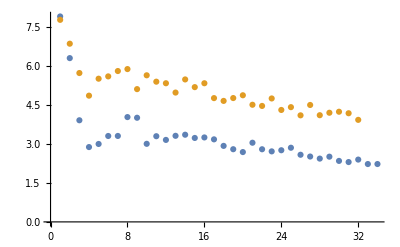

```mathematica
ListPlot[{test10data, train10data}]
```

```mathematica
newtest10data = {7.931473255157471,7.910677433013916,7.893889427185059,7.87094259262085,7.84145975112915,7.8037896156311035,7.747678756713867,7.670152187347412,7.552892684936523,7.374253749847412,7.226692199707031,7.083413124084473,6.975493431091309,6.862679481506348,6.788094997406006,6.668817520141602,6.59330415725708,6.528772830963135,6.445667743682861,6.377239227294922,6.28801155090332,6.256349563598633,6.225033283233643,6.225903034210205}
```

{7.93147,7.91068,7.89389,7.87094,7.84146,7.80379,7.74768,7.67015,7.55289,7.37425,7.22669,7.08341,6.97549,6.86268,6.78809,6.66882,6.5933,6.52877,6.44567,6.37724,6.28801,6.25635,6.22503,6.2259}

```mathematica
newtrain10data = {7.9397634974740114,7.905387134744087,7.886019969440042,7.848714395532593,7.824053856550295,7.774324811165526,7.69815212741594,7.581362489041768,7.39720493294476,7.215954419739679,7.075362216452688,6.96632305721265,6.856263156521203,6.763435534357203,6.616959922640756,6.529066660555544,6.424450745675906,6.392775823894958,6.248309543429464,6.258387826423116,6.120293376900846,6.0316282388807325}
```

{7.93976,7.90539,7.88602,7.84871,7.82405,7.77432,7.69815,7.58136,7.3972,7.21595,7.07536,6.96632,6.85626,6.76344,6.61696,6.52907,6.42445,6.39278,6.24831,6.25839,6.12029,6.03163}

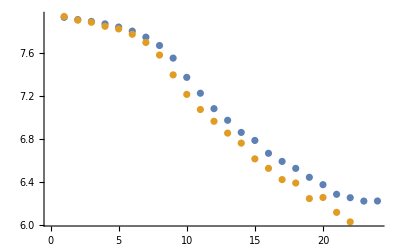

```mathematica
ListPlot[{newtest10data, newtrain10data}]
```

```mathematica
testsensitivedata = {7.9752044677734375,7.966643333435059,7.937247276306152,7.917086601257324,7.888258457183838,7.838900566101074,7.753513813018799,7.643852233886719,7.5380682945251465,7.427278995513916,7.326283931732178,7.231266975402832,7.170930862426758,7.0152411460876465,6.929738521575928,6.845309257507324,5.258999347686768,4.847535133361816,4.569896221160889,4.61682653427124,4.302250385284424,4.147897720336914,3.889040946960449,3.6132850646972656,3.773218870162964,3.75553297996521,3.551595687866211,3.524376153945923,3.7258198261260986,3.2113254070281982,3.1850194931030273,3.347956418991089,3.3555657863616943,2.5322587490081787,2.7834510803222656,2.46368670463562,2.4270846843719482,2.1024038791656494,1.9937934875488281,2.005767583847046,1.8250441551208496,1.903817057609558,1.8096336126327515,1.8199833631515503,1.8105695247650146,1.7337905168533325,1.6611790657043457,1.7399364709854126,1.630602240562439,1.611074447631836,1.5731313228607178,1.4782416820526123,1.334665298461914,1.376860499382019,1.3164772987365723,1.293295979499817,1.390343189239502,1.3436753749847412,1.4707682132720947,1.463808536529541,1.4039406776428223,1.3965232372283936,1.4501011371612549,1.323099136352539,1.3153197765350342,1.317671298980713,1.3860642910003662,1.4527578353881836,1.2637971639633179,1.2856485843658447,1.3035171031951904,1.3403366804122925,1.235256552696228,1.404137134552002,1.1842076778411865,1.3350350856781006,1.2443294525146484,1.245492696762085,1.255738377571106,1.2372957468032837,1.2496061325073242,1.3558127880096436,1.2678121328353882,1.28213632106781,1.2960700988769531,1.3251830339431763,1.3150228261947632,1.3129290342330933,1.3506542444229126,1.2481554746627808,1.230715274810791,1.2238460779190063,1.180526852607727,1.3418587446212769,1.3180546760559082,1.2899632453918457,1.390256643295288,1.270692229270935,1.308059811592102,1.3110392093658447,1.2855291366577148,1.3311865329742432,1.281554937362671,1.412939429283142,1.196828007698059,1.4943201541900635,1.8864704370498657,2.3381073474884033,2.213984251022339,2.6622250080108643,2.851050615310669,2.904649496078491,3.1086506843566895,3.039539337158203,3.0850627422332764,3.118251323699951,3.3666279315948486,3.4049465656280518,3.2608776092529297,3.5195116996765137,3.4017586708068848,3.2839672565460205,3.234567880630493,3.4276397228240967,3.4955966472625732,3.3192250728607178,3.387018918991089,3.2880492210388184,3.1453611850738525,3.2010395526885986,3.204643726348877,3.2067220211029053,3.1391937732696533,3.2322041988372803,3.2692010402679443,3.3654985427856445,3.2613611221313477,3.2941741943359375,3.278257369995117,3.4774115085601807,3.3110287189483643,3.118919849395752,3.371070146560669,3.434997081756592,3.262500524520874,3.1700189113616943,3.326195240020752,3.4171230792999268,3.361055612564087,3.3435134887695312,3.3728418350219727,3.4282829761505127,3.29101300239563,3.566152572631836,3.4231512546539307,3.3949739933013916,3.2812230587005615,3.4427809715270996,3.372103452682495,3.4607326984405518,3.374821186065674,3.440962553024292,3.4961564540863037,3.4298808574676514,3.5293452739715576,3.4841957092285156,3.6802611351013184,3.6288206577301025,3.6521708965301514,3.719503164291382,3.6777126789093018,3.3525187969207764,3.528367757797241,3.635775327682495,3.803900718688965,3.5288937091827393,3.704699993133545,3.6599419116973877,3.7717690467834473,3.801516532897949,3.8558266162872314,3.858203411102295,3.8041563034057617,3.7312874794006348,3.689356565475464,3.749610185623169,3.686426877975464,3.8178725242614746,3.9044289588928223,3.9648048877716064,3.9156932830810547,4.052257061004639,4.0617594718933105,3.924408197402954,4.182392597198486,4.120563983917236,4.203584671020508,4.256354808807373,4.241725444793701,4.13973331451416,4.333738327026367,4.121142864227295,4.306056976318359,4.06560754776001,4.345785617828369,4.146350383758545,4.178437232971191,4.351385593414307,4.654141902923584,4.279897212982178,4.7643818855285645,4.452162742614746,4.647940158843994,4.605763912200928,4.633248329162598,4.517313003540039,4.664196491241455,4.803779602050781,4.714829444885254,4.4997944831848145,4.584878921508789,4.808554649353027,4.627010345458984,4.721689224243164,4.848136901855469,4.801998615264893,4.807588577270508,4.718164443969727,4.945136070251465,4.958154678344727,4.967016220092773,4.928672790527344,5.00325345993042,4.994667053222656,4.889060020446777,4.87692403793335,5.076712608337402,4.903973579406738,4.932130813598633,5.141913414001465,5.279413223266602,5.224006652832031,4.894279479980469,5.104556560516357,5.240092754364014,5.167275428771973,5.115592002868652,5.200652122497559,5.29799747467041,5.160220146179199,5.105515480041504,5.277887344360352,5.328211784362793,5.034226417541504,5.1011176109313965,5.208924293518066,5.277819633483887,5.181591510772705,5.353893280029297,5.228665828704834,5.446147441864014,5.236959934234619,5.172371864318848,5.18229341506958,5.344153881072998,5.352280616760254,5.243490695953369,5.434996128082275,5.363683223724365,5.498158931732178,5.411909580230713,5.320816993713379,5.313685417175293,5.47395658493042,5.509908199310303,5.52515172958374,5.219611167907715,5.007925033569336,5.244225978851318,5.454014301300049,5.421370029449463,5.481902122497559,5.389529228210449,5.348028659820557,5.4325995445251465,5.4089226722717285,5.409327507019043,5.239505290985107,5.539730548858643,5.476532459259033,5.627819538116455,5.515598773956299,5.327256202697754,5.4375,5.4283599853515625,5.578703880310059,5.57335901260376,5.628410339355469,5.574877738952637,5.495962619781494,5.475355625152588,5.4954328536987305,5.403957843780518,5.63210916519165,5.652597427368164,5.618486404418945,5.659140110015869,5.939916133880615,5.36829137802124,5.7106828689575195,5.405540466308594,5.458304405212402,5.601410865783691,5.687027454376221,5.5520830154418945,5.686743259429932,5.799543380737305,5.796461582183838,5.864343166351318,5.424142360687256,5.69927978515625,5.523233413696289,5.64698600769043,5.597519397735596,5.763519287109375,5.8079047203063965,5.694319725036621,5.578772068023682,5.6366143226623535,5.691038608551025,5.815109729766846,5.748520851135254,5.963155269622803,5.883754253387451,5.673789024353027,5.739931583404541,6.164195537567139,5.664802551269531,5.63999605178833,5.726881980895996,5.684932708740234,5.628556251525879,5.795123100280762,5.731960296630859,5.775851726531982,5.696838855743408,5.831880569458008,5.790621757507324,5.584022045135498,5.707507133483887,5.740487575531006,5.733103275299072,5.785782814025879,5.796706199645996,5.734106540679932,5.780755519866943,5.558938980102539,5.806774139404297,6.051479816436768,5.7463579177856445,5.709417819976807,5.742035388946533,6.052021503448486,5.5196709632873535,5.584644794464111,5.893784046173096,5.941356658935547,5.496081829071045,5.83785343170166,5.793468475341797,5.826248645782471,6.126988410949707,5.8836212158203125,5.8765549659729,5.726081848144531,5.767983913421631,5.82534122467041,5.817628860473633,5.793101787567139,5.8793206214904785,5.638524532318115,5.6378021240234375,5.849905967712402,5.709704875946045,5.531584739685059,5.796103000640869,5.8237504959106445,5.72675085067749,5.475510597229004,5.839521884918213,5.816961765289307,5.803765773773193,5.710979461669922,5.801411151885986,5.908321380615234,5.559581279754639,5.8173508644104,6.100321292877197,5.809995651245117,5.820694446563721,5.863283157348633,5.952040195465088,5.690018177032471,5.969879627227783,5.931796550750732,5.7815165519714355,5.88379430770874,5.639901161193848,5.9747314453125,5.692793846130371,6.014607906341553,5.460179328918457,5.92986536026001,5.754251480102539,6.026901721954346,5.813562870025635,5.947193622589111,5.8045573234558105,5.492732524871826,6.058342933654785,6.054207801818848,5.6281914710998535,5.704540729522705,5.778037071228027,5.953474044799805,5.831972599029541,5.824557304382324,5.699740409851074,5.598649024963379,5.761174201965332,5.826071739196777,5.780978679656982,5.870283603668213,5.918684005737305,6.1042399406433105,5.841818809509277,5.762088298797607,5.7903923988342285,5.579721927642822,5.751293659210205,5.671105861663818,5.668398857116699,5.830920219421387,5.907206058502197,5.849082946777344,5.714575290679932,5.859736919403076,5.984081745147705,5.821806907653809,5.880168914794922,5.789030075073242,5.584460735321045,5.964138507843018,5.964085102081299}
```

{7.9752,7.96664,7.93725,7.91709,7.88826,7.8389,7.75351,7.64385,7.53807,7.42728,7.32628,7.23127,7.17093,7.01524,6.92974,6.84531,5.259,4.84754,4.5699,4.61683,4.30225,4.1479,3.88904,3.61329,3.77322,3.75553,3.5516,3.52438,3.72582,3.21133,3.18502,3.34796,3.35557,2.53226,2.78345,2.46369,2.42708,2.1024,1.99379,2.00577,1.82504,1.90382,1.80963,1.81998,1.81057,1.73379,1.66118,1.73994,1.6306,1.61107,1.57313,1.47824,1.33467,1.37686,1.31648,1.2933,1.39034,1.34368,1.47077,1.46381,1.40394,1.39652,1.4501,1.3231,1.31532,1.31767,1.38606,1.45276,1.2638,1.28565,1.30352,1.34034,1.23526,1.40414,1.18421,1.33504,1.24433,1.24549,1.25574,1.2373,1.24961,1.35581,1.26781,1.28214,1.29607,1.32518,1.31502,1.31293,1.35065,1.24816,1.23072,1.22385,1.18053,1.34186,1.31805,1.28996,1.39026,1.27069,1.30806,1.31104,1.28553,1.33119,1.28155,1.41294,1.19683,1.49432,1.88647,2.33811,2.21398,2.66223,2.85105,2.90465,3.10865,3.03954,3.08506,3.11825,3.36663,3.40495,3.26088,3.51951,3.40176,3.28397,3.23457,3.42764,3.4956,3.31923,3.38702,3.28805,3.14536,3.20104,3.20464,3.20672,3.13919,3.2322,3.2692,3.3655,3.26136,3.29417,3.27826,3.47741,3.31103,3.11892,3.37107,3.435,3.2625,3.17002,3.3262,3.41712,3.36106,3.34351,3.37284,3.42828,3.29101,3.56615,3.42315,3.39497,3.28122,3.44278,3.3721,3.46073,3.37482,3.44096,3.49616,3.42988,3.52935,3.4842,3.68026,3.62882,3.65217,3.7195,3.67771,3.35252,3.52837,3.63578,3.8039,3.52889,3.7047,3.65994,3.77177,3.80152,3.85583,3.8582,3.80416,3.73129,3.68936,3.74961,3.68643,3.81787,3.90443,3.9648,3.91569,4.05226,4.06176,3.92441,4.18239,4.12056,4.20358,4.25635,4.24173,4.13973,4.33374,4.12114,4.30606,4.06561,4.34579,4.14635,4.17844,4.35139,4.65414,4.2799,4.76438,4.45216,4.64794,4.60576,4.63325,4.51731,4.6642,4.80378,4.71483,4.49979,4.58488,4.80855,4.62701,4.72169,4.84814,4.802,4.80759,4.71816,4.94514,4.95815,4.96702,4.92867,5.00325,4.99467,4.88906,4.87692,5.07671,4.90397,4.93213,5.14191,5.27941,5.22401,4.89428,5.10456,5.24009,5.16728,5.11559,5.20065,5.298,5.16022,5.10552,5.27789,5.32821,5.03423,5.10112,5.20892,5.27782,5.18159,5.35389,5.22867,5.44615,5.23696,5.17237,5.18229,5.34415,5.35228,5.24349,5.435,5.36368,5.49816,5.41191,5.32082,5.31369,5.47396,5.50991,5.52515,5.21961,5.00793,5.24423,5.45401,5.42137,5.4819,5.38953,5.34803,5.4326,5.40892,5.40933,5.23951,5.53973,5.47653,5.62782,5.5156,5.32726,5.4375,5.42836,5.5787,5.57336,5.62841,5.57488,5.49596,5.47536,5.49543,5.40396,5.63211,5.6526,5.61849,5.65914,5.93992,5.36829,5.71068,5.40554,5.4583,5.60141,5.68703,5.55208,5.68674,5.79954,5.79646,5.86434,5.42414,5.69928,5.52323,5.64699,5.59752,5.76352,5.8079,5.69432,5.57877,5.63661,5.69104,5.81511,5.74852,5.96316,5.88375,5.67379,5.73993,6.1642,5.6648,5.64,5.72688,5.68493,5.62856,5.79512,5.73196,5.77585,5.69684,5.83188,5.79062,5.58402,5.70751,5.74049,5.7331,5.78578,5.79671,5.73411,5.78076,5.55894,5.80677,6.05148,5.74636,5.70942,5.74204,6.05202,5.51967,5.58464,5.89378,5.94136,5.49608,5.83785,5.79347,5.82625,6.12699,5.88362,5.87655,5.72608,5.76798,5.82534,5.81763,5.7931,5.87932,5.63852,5.6378,5.84991,5.7097,5.53158,5.7961,5.82375,5.72675,5.47551,5.83952,5.81696,5.80377,5.71098,5.80141,5.90832,5.55958,5.81735,6.10032,5.81,5.82069,5.86328,5.95204,5.69002,5.96988,5.9318,5.78152,5.88379,5.6399,5.97473,5.69279,6.01461,5.46018,5.92987,5.75425,6.0269,5.81356,5.94719,5.80456,5.49273,6.05834,6.05421,5.62819,5.70454,5.77804,5.95347,5.83197,5.82456,5.69974,5.59865,5.76117,5.82607,5.78098,5.87028,5.91868,6.10424,5.84182,5.76209,5.79039,5.57972,5.75129,5.67111,5.6684,5.83092,5.90721,5.84908,5.71458,5.85974,5.98408,5.82181,5.88017,5.78903,5.58446,5.96414,5.96409}

```mathematica
trainsensitivedata = {7.96844571397954,7.95615744981965,7.919671997277184,7.904761171819736,7.8560048495656005,7.783759812245449,7.68646192496358,7.569063464514764,7.455547325942867,7.324251295398348,7.233651270000686,7.12061771956022,7.009098265482043,6.88750781051451,6.821329492665856,6.514761187163247,6.054209190781051,5.862136439173711,5.711746543642513,5.657612463078775,5.1493862234620655,5.366659748338378,5.274829373586863,5.071095456462669,5.064231927706677,4.897397759332463,4.7860165860463715,5.155616513547793,4.80051651263042,4.426658046711812,4.664409954554786,4.791705520247698,4.230394193991251,4.072451744554029,4.4441081369554665,4.053008134089529,3.9562938233544975,3.871263742121998,4.028984003114553,3.865779297184584,3.9618559405017497,3.6785713997745404,3.3911824051498884,3.5630550618967733,3.4215692741425356,3.1778905914656104,3.1541946293071628,3.480823855831363,3.3408031547352564,3.4571580087280296,3.2668437086651094,3.2264196732381407,3.3264920898370693,3.4471118893258192,3.1910581744302555,3.1972831616589095,3.1126568264498284,3.3724849974425535,2.983680174747893,2.9222450325298395,3.410880896404441,3.1256933842853556,3.033447673613665,2.7376246888286033,3.0857013080140683,3.517921216082588,3.5098329035996354,3.0767153491475745,2.7396200949767575,2.833314320759115,3.2172026230321342,2.9428219171092804,3.1992273833760403,3.0847019687081825,3.438250944733427,3.0813240413929255,3.0877217867302864,2.974523064807763,3.36717325736166,3.259999502589346,3.0787097101028746,2.832613024791684,3.2349646491461943,3.333810515763883,3.033265168069738,3.058018126922386,3.1330241354244364,2.7727409776890743,3.181549636432795,2.8917220436879485,3.069502270950919,3.178531687317726,2.903239986705616,3.195680430037389,2.907251654895232,3.132956389874206,2.784257546030621,3.0493239826724046,2.9263691860016077,3.4118337281283546,2.8729773562128633,3.2552664512261003,2.7130464994027785,3.0041176552327737,2.857941273823505,3.0518026860362806,3.3750178964608697,3.2714536077098897,3.629217529249093,3.5192478442004,3.6166443610161307,3.669866792085898,3.772021526894251,3.7433710043238673,3.7926717751569163,3.770231411207529,3.837427339139558,3.8446079282418752,3.956353903519839,3.9128497493167824,3.8101132462648946,4.026983379694194,4.004761818403765,4.101930981949027,3.8570355152695974,3.8552385131843807,3.9433667608845404,3.782630878045453,3.599085226741538,3.7929057494961507,3.721834127217877,3.509769096370584,4.0085705811188515,3.6507954206260003,3.717887513648139,3.8015326958382167,3.8047650728214673,3.779225716528466,3.7775854484939884,3.958686432898183,3.8818007104232066,3.856186526314906,3.877154066025019,4.125749106932819,4.002312871278167,3.8648481406747495,4.012556404288488,3.6825680550083972,3.772430092284891,3.8075511443860304,3.7966464320266744,3.8835913280034062,3.8445261911181374,3.8913174402166546,3.8895595603879127,3.9168277958316766,3.7649134784776233,3.930638847291024,3.940947779208079,3.8385360156961066,3.7121007844963696,3.8205494131955415,3.852326612036346,3.832397882998909,3.894460300013307,3.802217700785442,4.121363471833001,3.9259500904798283,4.004395397216526,3.979966399922444,3.8954107777756213,3.9341009043227633,3.6637685044594637,3.789389180499358,3.739434050884805,3.7673865763614898,3.93986087518093,4.166866262976215,4.146480288046408,3.7512306244659466,3.9157144077819495,3.9260362805662488,4.029946721473657,3.9621248854202644,3.813578161580175,4.0053581161561445,4.032833986024687,3.844499487703855,3.987925071215472,3.9034638911179225,3.9432511117253166,3.9017422238899524,4.04990016764614,4.025174352859167,4.128587801502551,4.03562710028359,4.111184269607333,3.961155496428982,3.940804570430924,4.009332523942393,4.255448233935739,4.272263589407464,3.8578738285769036,4.15854353374923,4.0528145151164585,3.993440695137597,4.018155337000509,4.136350978102386,4.216741194721147,4.109386157375113,4.0957385583106145,4.070699310526225,4.125769596021042,4.083326133283894,4.19022563494454,4.002941090523867,4.2211823473969625,4.205358971877908,4.191082656460589,4.300102223925619,4.232991971930639,4.203995008542519,4.118780263663718,4.059974823439718,4.339030993286213,4.279797648219503,4.063862671228393,4.150309138891026,4.10940304327229,4.129906758979137,4.241266442362656,4.34568221303994,4.0700018323165,4.204300603580847,4.293745000064146,4.2952707322005095,4.245292798231896,4.295447184736407,4.192365276623168,4.187495217109182,4.274964098666716,4.121393168155695,4.168765324992117,4.42450064896466,4.296122848834097,4.269162969929893,4.231588177501135,4.333501231714999,4.23406930478827,4.1226501131566975,4.049162465025514,4.357923965851594,4.0587836195294535,4.371117780059307,4.23258862114477,4.299374389755278,4.251267862864382,4.177731266873153,4.217381995840577,4.251380112635926,4.105774674949401,4.364190410738763,4.389752662737513,4.1547634158250855,4.191510681859564,4.306651243209227,4.318635232209362,4.304172926683936,4.143135632430747,4.364071508984216,4.234228672664301,4.290551689082484,4.14437909037122,4.25184528791608,4.181932453834496,4.27531016288998,4.298213012079104,4.222525250753671,4.100734734941072,4.139082965017962,4.365620877033185,4.237954605870837,4.163660422255055,4.232539795068255,4.340533830523762,4.289633048765858,4.156975859076901,4.377711373418623,4.184725061284252,4.2074327034987355,4.194576584087704,4.241738589858832,4.311835865933076,4.28121183832826,4.159467282897573,4.286575389365246,4.3501828101999545,4.329487220725783,4.287255318160189,4.2579648322549986,4.340657067788155,4.469733441379979,4.134728338100779,4.265936865599717,4.2843234304571,4.123359288312233,4.251481556883473,4.255017314883303,4.389442613186281,4.296561695228182,4.187011594869603,4.410964147861568,4.419339567153109,4.155094068921233,4.306425772486717,4.20939200320114,4.189811387949978,4.320908279382501,4.273651042990747,4.308803119616117,4.167714574879756,4.2674451190460765,4.340202013701905,4.2281355130824885,4.136068311476723,4.032228056888403,4.370807252552245,4.28503465210282,4.447038339137237,4.137364381693354,4.443871550553704,4.353270185553821,4.187295665014652,4.127069672600327,4.052040630138624,3.867269986908919,4.197165338414402,4.242955696776535,4.204009111508415,4.250271794159698,4.074168208570127,4.3614711930042125,4.126939183560514,4.177727792667138,4.248919744785021,4.158474535000297,4.324641356139749,4.210728422870733,4.313144599654985,4.2809240235756,4.397218549340623,4.2778726976536845,4.308926114418336,4.289843564334964,4.220203933413905,4.139424786204716,4.325231084176081,4.181908044772144,4.1383503840798115,4.278360495964125,4.397716185671289,4.212921165374839,4.240001195264785,4.215461491164517,4.325494064283898,4.212482127185876,4.200688197981767,4.123597176884012,4.325163879395972,4.196471285343395,4.340914000795788,4.286184806507118,4.152835352177427,4.117988865321018,4.293732478296158,4.18942966633282,4.229104476938713,4.182637903264924,4.4082114774164465,4.182939225161715,4.103388591142187,4.217444641704697,4.304658960514641,4.209983412402358,4.252705756799853,4.303156865843994,4.23668682764778,4.435422925009793,4.060419340478707,4.374163022001131,4.285144903728095,4.181678214143238,4.157417307724291,4.069464589558548,3.939627607360338,4.22461179078479,4.430645175542969,4.262804657790463,4.263398432438542,4.053664067609748,4.287658091161456,4.318954732364406,4.207951967883682,4.1898661660951655,4.168703690650629,4.249067641705776,4.181202750309013,4.239421961651884,4.273596655184482,4.422480074012939,4.250235278924895,4.117793530503253,4.261369616495929,4.358622940332081,4.282193334605115,4.268816416801135,4.098604368287115,4.271570097663157,4.0770053424146075,4.303813307980236,4.239404883635513,4.144254065574967,4.188139270927827,4.3162165262607415,4.025741422533399,4.209772117067476,4.141714504856568,4.230463110277578,4.299448630701356,4.016397393877958,4.330583152665925,4.225696949251286,4.102048076008928,4.251589000786912,3.95053382569382,4.449652264161836,4.25334023631979,4.075215305408165,4.26259122827006,4.227905819714583,4.333351508388755,4.239759637157818,4.195718303189463,4.252458465847753,4.270473267810797,4.317744679958879,4.256845258953254,4.0935267792019525,4.203246733893346,4.213755527550018,4.041946598826237,4.288052637035168}
```

{7.96845,7.95616,7.91967,7.90476,7.856,7.78376,7.68646,7.56906,7.45555,7.32425,7.23365,7.12062,7.0091,6.88751,6.82133,6.51476,6.05421,5.86214,5.71175,5.65761,5.14939,5.36666,5.27483,5.0711,5.06423,4.8974,4.78602,5.15562,4.80052,4.42666,4.66441,4.79171,4.23039,4.07245,4.44411,4.05301,3.95629,3.87126,4.02898,3.86578,3.96186,3.67857,3.39118,3.56306,3.42157,3.17789,3.15419,3.48082,3.3408,3.45716,3.26684,3.22642,3.32649,3.44711,3.19106,3.19728,3.11266,3.37248,2.98368,2.92225,3.41088,3.12569,3.03345,2.73762,3.0857,3.51792,3.50983,3.07672,2.73962,2.83331,3.2172,2.94282,3.19923,3.0847,3.43825,3.08132,3.08772,2.97452,3.36717,3.26,3.07871,2.83261,3.23496,3.33381,3.03327,3.05802,3.13302,2.77274,3.18155,2.89172,3.0695,3.17853,2.90324,3.19568,2.90725,3.13296,2.78426,3.04932,2.92637,3.41183,2.87298,3.25527,2.71305,3.00412,2.85794,3.0518,3.37502,3.27145,3.62922,3.51925,3.61664,3.66987,3.77202,3.74337,3.79267,3.77023,3.83743,3.84461,3.95635,3.91285,3.81011,4.02698,4.00476,4.10193,3.85704,3.85524,3.94337,3.78263,3.59909,3.79291,3.72183,3.50977,4.00857,3.6508,3.71789,3.80153,3.80477,3.77923,3.77759,3.95869,3.8818,3.85619,3.87715,4.12575,4.00231,3.86485,4.01256,3.68257,3.77243,3.80755,3.79665,3.88359,3.84453,3.89132,3.88956,3.91683,3.76491,3.93064,3.94095,3.83854,3.7121,3.82055,3.85233,3.8324,3.89446,3.80222,4.12136,3.92595,4.0044,3.97997,3.89541,3.9341,3.66377,3.78939,3.73943,3.76739,3.93986,4.16687,4.14648,3.75123,3.91571,3.92604,4.02995,3.96212,3.81358,4.00536,4.03283,3.8445,3.98793,3.90346,3.94325,3.90174,4.0499,4.02517,4.12859,4.03563,4.11118,3.96116,3.9408,4.00933,4.25545,4.27226,3.85787,4.15854,4.05281,3.99344,4.01816,4.13635,4.21674,4.10939,4.09574,4.0707,4.12577,4.08333,4.19023,4.00294,4.22118,4.20536,4.19108,4.3001,4.23299,4.204,4.11878,4.05997,4.33903,4.2798,4.06386,4.15031,4.1094,4.12991,4.24127,4.34568,4.07,4.2043,4.29375,4.29527,4.24529,4.29545,4.19237,4.1875,4.27496,4.12139,4.16877,4.4245,4.29612,4.26916,4.23159,4.3335,4.23407,4.12265,4.04916,4.35792,4.05878,4.37112,4.23259,4.29937,4.25127,4.17773,4.21738,4.25138,4.10577,4.36419,4.38975,4.15476,4.19151,4.30665,4.31864,4.30417,4.14314,4.36407,4.23423,4.29055,4.14438,4.25185,4.18193,4.27531,4.29821,4.22253,4.10073,4.13908,4.36562,4.23795,4.16366,4.23254,4.34053,4.28963,4.15698,4.37771,4.18473,4.20743,4.19458,4.24174,4.31184,4.28121,4.15947,4.28658,4.35018,4.32949,4.28726,4.25796,4.34066,4.46973,4.13473,4.26594,4.28432,4.12336,4.25148,4.25502,4.38944,4.29656,4.18701,4.41096,4.41934,4.15509,4.30643,4.20939,4.18981,4.32091,4.27365,4.3088,4.16771,4.26745,4.3402,4.22814,4.13607,4.03223,4.37081,4.28503,4.44704,4.13736,4.44387,4.35327,4.1873,4.12707,4.05204,3.86727,4.19717,4.24296,4.20401,4.25027,4.07417,4.36147,4.12694,4.17773,4.24892,4.15847,4.32464,4.21073,4.31314,4.28092,4.39722,4.27787,4.30893,4.28984,4.2202,4.13942,4.32523,4.18191,4.13835,4.27836,4.39772,4.21292,4.24,4.21546,4.32549,4.21248,4.20069,4.1236,4.32516,4.19647,4.34091,4.28618,4.15284,4.11799,4.29373,4.18943,4.2291,4.18264,4.40821,4.18294,4.10339,4.21744,4.30466,4.20998,4.25271,4.30316,4.23669,4.43542,4.06042,4.37416,4.28514,4.18168,4.15742,4.06946,3.93963,4.22461,4.43065,4.2628,4.2634,4.05366,4.28766,4.31895,4.20795,4.18987,4.1687,4.24907,4.1812,4.23942,4.2736,4.42248,4.25024,4.11779,4.26137,4.35862,4.28219,4.26882,4.0986,4.27157,4.07701,4.30381,4.2394,4.14425,4.18814,4.31622,4.02574,4.20977,4.14171,4.23046,4.29945,4.0164,4.33058,4.2257,4.10205,4.25159,3.95053,4.44965,4.25334,4.07522,4.26259,4.22791,4.33335,4.23976,4.19572,4.25246,4.27047,4.31774,4.25685,4.09353,4.20325,4.21376,4.04195,4.28805}

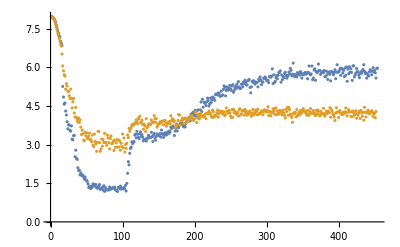

```mathematica
ListPlot[{testsensitivedata, trainsensitivedata}]
```

```mathematica
train500data = {7.748741181237772,7.7182284630912354,7.687637100624486,7.669043148148316,7.623098474575011,7.527852008240131,7.457684630898793,7.31359373062066,7.158935079484898,7.0528868616996885,6.921970818946226,6.800107320466041,6.739925004529564,6.647547806759629,6.500228641424876,6.447842658772232,6.357901987253192,6.3399233485655335,6.2489290911078506,6.215141950869847,6.16114321434329,6.082035791449985,6.016363219205976,5.906724477728747,5.9379975642795815,5.9110855116355365,5.834290814522117,5.833776083195577,5.7455910861855966,5.677739934755579,5.7089249188362965,5.676189294320853,5.6545581657815225,5.577819325437182,4.928750840788484,4.178003430540734,3.9322088721245323,3.717511316320836,3.603390452911841,3.950426221860109,3.6186246419501304,3.7517285397112623,3.6836201422562986,3.7727898315509365,4.00385041462588,4.105273807075409,4.089414749356459,4.24627384674475,4.183275128980513,4.350526497554509,4.28789080138799,4.252085707870965,4.1469786279784575,3.870069603864026,4.048372747198116,3.85564103955085,4.081088444996154,4.139174384342901,4.105459370660756,3.9664959951907885,3.7875738563332892,3.9203158751737215,3.9026292899172903,3.9335263153161066,4.238570487894489,3.936868953580007,3.812030098798946,3.6453694907309773,3.70898184024717,3.987747028635882,3.578912350389018,3.799475737242343,3.5718396266607395,3.692940448771669,3.672253402056222,3.7569262034682334,3.5005938019152176,3.5953247821760828,3.6892639570909678,3.598927378595487,3.8672960350139998,3.501307470986765,3.6711419269880357,3.396112538767876,3.747280215966931,3.440228316189191,3.4416000879236126,3.595680972862537,3.7988648918159362,3.2742046346746334,3.6247810956779563,3.3966647665043372,3.5223286849877398,3.543357426368958,3.259723341669982,3.638566507467562,3.6012689030419374,3.272146579283024,3.6574609708251056,3.404444791206568,3.46373514530361,3.283746859742,3.353630937479315,3.4451325518538467,3.530367825878345,3.451301016609147,3.2310507756230784,3.513565714925136,3.9745183592825013,3.507280999376913,3.251616828309392,3.4002289614565298,3.165507621933345,3.264684218388005,3.3386627718922166,3.6840858715989797,3.349634581208786,3.5783526968535533,3.2327265541993118,3.19798362345081,3.32839021263557,3.20887307970503,3.2079044831134604,3.50668945384701,3.4033927061142735,3.7584467750487915,3.369621286740409,3.1387312628750528,3.025231047785274,2.8855386869519544,3.056235343411885,3.5373486556292404,3.3850760934800626,2.99122339681537,3.3461278425454335,2.9024126215772457,3.2999787579968274,3.425094156892519,3.293683848705308,3.2019646685541123,3.11474233133875,3.1925158898247226,3.3270422073706776,2.6947204727209497,2.975058700174303,3.0153202918417144,3.4688615477838365,2.9287978636654888,3.036062687285528,2.864128459354293,3.0771398084733277,3.1741658909289687,3.1575073917695664,3.0100230278769247,2.5114915050208455,2.756894895372527,3.2894892244646377,2.9007172141960123,3.1179802278312723,2.96258486684086,2.703958280939389,2.6342346701137296,3.3272453363883483,2.981014373735757,3.0512519077107187,3.1092669760716958,2.9111097676205895,2.8316518816420366,2.7561165720215275,2.880812902309085,2.7375053971762866,2.7282875361172874,3.1830270597844903,3.1278097966255127,2.6958425602033533,3.052136881952701,2.7765897522906973,2.8888253892661497,2.75229839693634,2.930314688127238,2.9139362764866816,2.7949107598093614,2.7126096552343157,3.023826595957394,2.917708891802117,2.891487058811522,2.8491910295903526,2.930260038611586,2.689883046918099,2.9685246626785426,2.8706831544373763,3.086220328344206,2.824631100582891,2.8194056375828978,2.734274455337837,2.766738784258432,2.8346942855512345,3.0476097428687985,2.8794598853257387,2.9970538435256926,3.129243491191262,2.984696623875384,3.12184821951944,2.6260933257476875,3.1355661615097614,3.1072184466277184,3.028539343654408,2.9678651610114013,2.6227498891179795,3.038549342429821,2.812535312135966,3.114075118591772,3.0233495535676993,2.8186270976518553,2.7813469701669056,2.9746226332110575,2.9263763236184372,2.9287920413547557,2.831984884398367,2.9779533687776634,2.848133442893948,3.055210333994897,3.0082469372080776,3.173118099755665,2.9192698724374875,2.879072092964666,2.9617375903986227,3.0406878981563836,3.1439597194862934,2.998379633393145,2.9446861583286035,2.9887080388414398,2.7715759298879927,2.848493791623592,3.2897147933520547,3.114962646346269,2.8373525596804323,2.781157639689163,2.7294568957182395,2.7736234692321022,3.3539378030120583,2.6736166664526575,2.8014032715832218,2.8850047273782913,3.0279180623518953,2.674816719863316,2.7044026021234875,2.8026965551177416,2.6586599658744525,2.8678156252469584,2.3004333473590415,2.569689628959355,2.8989302867836257,2.841193729625638,2.7194913463572696,2.9013913743044157,2.8818244063617957,2.9939538450115752,2.6372892849550684,2.741193414266144,2.208925915785457,2.6541745531122665,2.710504249677119,2.727342578295082,2.7058041996447035,2.390637711958565,2.65750068263332,2.513548796716302,2.547931040428124,2.7239603469931355,2.72056129752471,2.705488074187883,2.6852049939705234,2.5895493378664454,2.61836252052309,2.777174071035901,2.621910583729065,2.6424302846729795,2.758764880914612,2.711446225353228,2.801370796665796,2.6657615350728063,2.809789905380705,2.485535875162906,2.823445368481819,2.395068454923043,2.784646336467842,2.1778068188710695,2.4982902154147357,2.4700381306645944,2.5699090551854646,2.2902992499961132,2.584683961587369,2.4292291139235243,2.709652012710866,2.897827321160401,2.733794902833685,2.205167159713789,2.6136309642134625,2.8543441653021744,2.757585595559159,2.225764284049643,2.651882123376719,2.403871717524239,2.5941246336687906,2.418996599727688,2.554526721218787,2.607434526416118,2.1315979906831917,2.7219122982649173,3.1029034718949235,2.6176349682078954,2.611419098559762,2.7102884425711085,2.792398454290945,2.8038185711635935,2.631750499132537,2.9241061488543085,2.556078170366541,2.534447020319055,2.683134585674194,2.895230824681079,2.525085807660334,2.480012740293925,2.27712764865602,2.715014023712549,2.394230142940975,2.48128990781547,2.4930069775361363,2.2040560438357817,2.576243931769117,2.474601794878589,2.5644319398279287,2.6310937697266428,2.359213861928665,2.4547477440715473,2.7046826128535746,2.4556684772760415,2.31869950487855,2.50882492811699,2.4625454680254473,2.7023335767333037,2.5370829602345513,2.5720654038330055,2.5460096395904674,2.6625592225617045,2.0323550925192864,2.986370593428751,2.525798125481303,2.347037747929842,2.326168199167123,2.5218054613182925,2.6466544234259266,2.5024959756517644,2.731553557152623,2.4413423938926715,2.482485789694225,2.9134083997208755,2.4136850613123406,2.6108071095919354,2.4637903474795366,2.680504289640078,2.5688241037244577,2.975172962567696,2.7027348039286436}
```

{7.74874,7.71823,7.68764,7.66904,7.6231,7.52785,7.45768,7.31359,7.15894,7.05289,6.92197,6.80011,6.73993,6.64755,6.50023,6.44784,6.3579,6.33992,6.24893,6.21514,6.16114,6.08204,6.01636,5.90672,5.938,5.91109,5.83429,5.83378,5.74559,5.67774,5.70892,5.67619,5.65456,5.57782,4.92875,4.178,3.93221,3.71751,3.60339,3.95043,3.61862,3.75173,3.68362,3.77279,4.00385,4.10527,4.08941,4.24627,4.18328,4.35053,4.28789,4.25209,4.14698,3.87007,4.04837,3.85564,4.08109,4.13917,4.10546,3.9665,3.78757,3.92032,3.90263,3.93353,4.23857,3.93687,3.81203,3.64537,3.70898,3.98775,3.57891,3.79948,3.57184,3.69294,3.67225,3.75693,3.50059,3.59532,3.68926,3.59893,3.8673,3.50131,3.67114,3.39611,3.74728,3.44023,3.4416,3.59568,3.79886,3.2742,3.62478,3.39666,3.52233,3.54336,3.25972,3.63857,3.60127,3.27215,3.65746,3.40444,3.46374,3.28375,3.35363,3.44513,3.53037,3.4513,3.23105,3.51357,3.97452,3.50728,3.25162,3.40023,3.16551,3.26468,3.33866,3.68409,3.34963,3.57835,3.23273,3.19798,3.32839,3.20887,3.2079,3.50669,3.40339,3.75845,3.36962,3.13873,3.02523,2.88554,3.05624,3.53735,3.38508,2.99122,3.34613,2.90241,3.29998,3.42509,3.29368,3.20196,3.11474,3.19252,3.32704,2.69472,2.97506,3.01532,3.46886,2.9288,3.03606,2.86413,3.07714,3.17417,3.15751,3.01002,2.51149,2.75689,3.28949,2.90072,3.11798,2.96258,2.70396,2.63423,3.32725,2.98101,3.05125,3.10927,2.91111,2.83165,2.75612,2.88081,2.73751,2.72829,3.18303,3.12781,2.69584,3.05214,2.77659,2.88883,2.7523,2.93031,2.91394,2.79491,2.71261,3.02383,2.91771,2.89149,2.84919,2.93026,2.68988,2.96852,2.87068,3.08622,2.82463,2.81941,2.73427,2.76674,2.83469,3.04761,2.87946,2.99705,3.12924,2.9847,3.12185,2.62609,3.13557,3.10722,3.02854,2.96787,2.62275,3.03855,2.81254,3.11408,3.02335,2.81863,2.78135,2.97462,2.92638,2.92879,2.83198,2.97795,2.84813,3.05521,3.00825,3.17312,2.91927,2.87907,2.96174,3.04069,3.14396,2.99838,2.94469,2.98871,2.77158,2.84849,3.28971,3.11496,2.83735,2.78116,2.72946,2.77362,3.35394,2.67362,2.8014,2.885,3.02792,2.67482,2.7044,2.8027,2.65866,2.86782,2.30043,2.56969,2.89893,2.84119,2.71949,2.90139,2.88182,2.99395,2.63729,2.74119,2.20893,2.65417,2.7105,2.72734,2.7058,2.39064,2.6575,2.51355,2.54793,2.72396,2.72056,2.70549,2.6852,2.58955,2.61836,2.77717,2.62191,2.64243,2.75876,2.71145,2.80137,2.66576,2.80979,2.48554,2.82345,2.39507,2.78465,2.17781,2.49829,2.47004,2.56991,2.2903,2.58468,2.42923,2.70965,2.89783,2.73379,2.20517,2.61363,2.85434,2.75759,2.22576,2.65188,2.40387,2.59412,2.419,2.55453,2.60743,2.1316,2.72191,3.1029,2.61763,2.61142,2.71029,2.7924,2.80382,2.63175,2.92411,2.55608,2.53445,2.68313,2.89523,2.52509,2.48001,2.27713,2.71501,2.39423,2.48129,2.49301,2.20406,2.57624,2.4746,2.56443,2.63109,2.35921,2.45475,2.70468,2.45567,2.3187,2.50882,2.46255,2.70233,2.53708,2.57207,2.54601,2.66256,2.03236,2.98637,2.5258,2.34704,2.32617,2.52181,2.64665,2.5025,2.73155,2.44134,2.48249,2.91341,2.41369,2.61081,2.46379,2.6805,2.56882,2.97517,2.70273}

```mathematica
test500data = {7.7620768547058105,7.744117259979248,7.713846683502197,7.681591033935547,7.656985282897949,7.611510753631592,7.52699089050293,7.3985915184021,7.249842166900635,7.119717597961426,6.997572898864746,6.919923305511475,6.801253795623779,6.731485366821289,6.659733772277832,6.573004722595215,6.507960319519043,6.435323715209961,6.36628532409668,6.322747707366943,6.27750301361084,6.210219383239746,6.170290470123291,6.094942569732666,6.084998607635498,6.081608772277832,5.993411064147949,5.960721492767334,5.907192707061768,5.848418235778809,5.8346266746521,5.830323219299316,5.750884532928467,5.706765174865723,5.701980113983154,2.8091847896575928,2.281860113143921,2.163813352584839,2.095463991165161,2.1433496475219727,2.2666819095611572,2.4547009468078613,2.526090145111084,2.5965518951416016,2.788670539855957,3.1595470905303955,2.96602725982666,3.406850576400757,3.3616158962249756,3.31459903717041,3.091996669769287,3.0609219074249268,2.9465415477752686,2.8573923110961914,2.8510079383850098,2.914116144180298,2.9288134574890137,2.813084363937378,2.910949230194092,2.6347475051879883,2.5187504291534424,2.8798916339874268,2.8558144569396973,2.9046127796173096,2.841348171234131,2.5804383754730225,2.528144598007202,2.5560989379882812,2.480586528778076,2.5327038764953613,2.4823408126831055,2.53387188911438,2.491837739944458,2.504408121109009,2.4892964363098145,2.5026893615722656,2.426589250564575,2.495687961578369,2.4074783325195312,2.3058903217315674,2.323688507080078,2.1868398189544678,2.3737218379974365,2.223924398422241,2.5049684047698975,2.167617082595825,2.239640235900879,2.387479782104492,2.3981242179870605,1.9504526853561401,2.2237396240234375,2.200615406036377,2.18843412399292,1.9968007802963257,1.9700003862380981,1.9132051467895508,1.962842345237732,1.9073562622070312,1.947603464126587,1.9195958375930786,2.0115811824798584,1.9865838289260864,1.9234085083007812,1.8728049993515015,1.8175641298294067,1.9719575643539429,2.008654832839966,1.9876571893692017,2.8404688835144043,1.94767165184021,2.0061845779418945,1.9412089586257935,1.9060570001602173,1.9678806066513062,1.9827229976654053,2.4187917709350586,1.9962468147277832,1.8429559469223022,1.8666949272155762,1.9945087432861328,1.913946509361267,1.9288686513900757,1.9788539409637451,2.041783571243286,1.9448513984680176,1.9046574831008911,4.754724025726318,2.024648904800415,1.9711089134216309,1.7987422943115234,1.8713724613189697,1.9123178720474243,1.9269046783447266,1.9711148738861084,1.910058856010437,2.091390609741211,1.8665132522583008,1.7711641788482666,1.5835164785385132,1.6639902591705322,1.614445447921753,1.50824773311615,1.511077880859375,1.4926913976669312,1.600520133972168,1.5048719644546509,1.5769329071044922,1.3633201122283936,1.5002385377883911,1.4201383590698242,1.343536376953125,1.4540985822677612,1.4248569011688232,1.3553344011306763,1.4316844940185547,1.4723438024520874,1.394809365272522,1.3585368394851685,1.3197532892227173,1.4672157764434814,1.3413114547729492,1.3254985809326172,1.419486403465271,1.2968449592590332,1.3276751041412354,1.3220360279083252,1.393491268157959,1.2989068031311035,1.310836672782898,1.3533896207809448,1.3971670866012573,1.4013036489486694,1.4164046049118042,1.3407222032546997,1.2958824634552002,1.3443948030471802,1.4058929681777954,1.408400058746338,1.3366670608520508,1.28602933883667,1.429033637046814,1.3328725099563599,1.3663136959075928,1.415313959121704,1.4106104373931885,1.4317339658737183,1.2893285751342773,1.3112114667892456,1.5286916494369507,1.354973554611206,1.3342849016189575,1.3787647485733032,1.3180644512176514,1.2731157541275024,1.3287971019744873,1.3240221738815308,1.4237306118011475,1.3715547323226929,1.4421393871307373,1.3958289623260498,1.3767045736312866,1.3376715183258057,1.412107229232788,1.425215244293213,1.3868476152420044,1.3535138368606567,1.357262372970581,1.3968067169189453,1.4072190523147583,1.4419692754745483,1.3718528747558594,1.4060918092727661,1.4766935110092163,1.4896022081375122,1.297542929649353,1.349466323852539,1.3366165161132812,1.3427475690841675,1.3161160945892334,1.405252456665039,1.2523307800292969,1.3083219528198242,1.3072583675384521,1.3825442790985107,1.4046741724014282,1.4188692569732666,1.441498041152954,1.364666223526001,1.3377941846847534,1.3999632596969604,1.3803156614303589,1.3797821998596191,1.3585361242294312,1.3775413036346436,1.369072675704956,1.303748369216919,1.3232873678207397,1.2980842590332031,1.4294967651367188,1.309816837310791,1.2418327331542969,1.2426711320877075,1.3445990085601807,1.2558262348175049,1.3320449590682983,1.1600327491760254,1.2185012102127075,1.3251656293869019,1.1340407133102417,1.1262593269348145,1.08990478515625,1.2996718883514404,1.1606452465057373,1.2418217658996582,1.093149185180664,1.1373414993286133,1.0572465658187866,1.1821891069412231,1.0230705738067627,1.0122568607330322,1.0660600662231445,1.10097074508667,1.067765712738037,1.051478624343872,1.0422439575195312,1.0311180353164673,0.9903686046600342,1.079351544380188,1.0006366968154907,0.8783886432647705,0.9030981063842773,0.8949446678161621,0.9682679176330566,0.8704199194908142,0.909405529499054,0.9052612781524658,1.04341459274292,0.9200533032417297,0.9125953912734985,0.883607804775238,0.8597804307937622,0.9553831815719604,0.8996194005012512,0.8797521591186523,0.8275426626205444,0.9636009335517883,0.9326552152633667,0.9203425049781799,0.7283030152320862,0.8777141571044922,0.9413981437683105,0.828843891620636,0.9139185547828674,0.8636463284492493,0.8555200695991516,0.8437631726264954,0.7634366154670715,0.8530585169792175,0.7599542140960693,0.8505374193191528,0.8021794557571411,0.9300430417060852,0.8258044719696045,0.8736020922660828,0.8487021327018738,0.8018152117729187,0.8469839096069336,0.8464506268501282,0.824166476726532,0.802632749080658,0.8359289169311523,0.8708798885345459,0.8934710621833801,0.877890944480896,0.8558424711227417,0.82818603515625,0.8263545632362366,0.8013886213302612,0.8157422542572021,0.88377845287323,0.8438171148300171,0.8052282333374023,0.8147501945495605,0.7737443447113037,0.8194863200187683,0.8177164196968079,0.8658586740493774,0.8279435038566589,0.8825936317443848,0.897508442401886,0.7917766571044922,0.796714186668396,0.8583871722221375,0.8048388957977295,0.9256223440170288,0.7410005331039429,0.9130138158798218,0.869507908821106,0.9861757159233093,0.9733937382698059,0.8873776197433472,0.9086925387382507,0.7947870492935181,0.8306288719177246,0.8492404222488403,0.8347910642623901,0.7853732109069824,0.8056821823120117,0.9272165298461914,0.7963735461235046,0.861702024936676,0.7920573353767395,0.9310397505760193,0.7812771797180176,0.8282026052474976,0.8492801785469055,0.8088974952697754,0.9128516316413879,0.7571619749069214,0.9082961678504944,0.8226931691169739,0.8170090913772583,0.8089911937713623,0.9705730676651001,0.8187702298164368,0.8549650311470032,0.854881763458252}
```

{7.76208,7.74412,7.71385,7.68159,7.65699,7.61151,7.52699,7.39859,7.24984,7.11972,6.99757,6.91992,6.80125,6.73149,6.65973,6.573,6.50796,6.43532,6.36629,6.32275,6.2775,6.21022,6.17029,6.09494,6.085,6.08161,5.99341,5.96072,5.90719,5.84842,5.83463,5.83032,5.75088,5.70677,5.70198,2.80918,2.28186,2.16381,2.09546,2.14335,2.26668,2.4547,2.52609,2.59655,2.78867,3.15955,2.96603,3.40685,3.36162,3.3146,3.092,3.06092,2.94654,2.85739,2.85101,2.91412,2.92881,2.81308,2.91095,2.63475,2.51875,2.87989,2.85581,2.90461,2.84135,2.58044,2.52814,2.5561,2.48059,2.5327,2.48234,2.53387,2.49184,2.50441,2.4893,2.50269,2.42659,2.49569,2.40748,2.30589,2.32369,2.18684,2.37372,2.22392,2.50497,2.16762,2.23964,2.38748,2.39812,1.95045,2.22374,2.20062,2.18843,1.9968,1.97,1.91321,1.96284,1.90736,1.9476,1.9196,2.01158,1.98658,1.92341,1.8728,1.81756,1.97196,2.00865,1.98766,2.84047,1.94767,2.00618,1.94121,1.90606,1.96788,1.98272,2.41879,1.99625,1.84296,1.86669,1.99451,1.91395,1.92887,1.97885,2.04178,1.94485,1.90466,4.75472,2.02465,1.97111,1.79874,1.87137,1.91232,1.9269,1.97111,1.91006,2.09139,1.86651,1.77116,1.58352,1.66399,1.61445,1.50825,1.51108,1.49269,1.60052,1.50487,1.57693,1.36332,1.50024,1.42014,1.34354,1.4541,1.42486,1.35533,1.43168,1.47234,1.39481,1.35854,1.31975,1.46722,1.34131,1.3255,1.41949,1.29684,1.32768,1.32204,1.39349,1.29891,1.31084,1.35339,1.39717,1.4013,1.4164,1.34072,1.29588,1.34439,1.40589,1.4084,1.33667,1.28603,1.42903,1.33287,1.36631,1.41531,1.41061,1.43173,1.28933,1.31121,1.52869,1.35497,1.33428,1.37876,1.31806,1.27312,1.3288,1.32402,1.42373,1.37155,1.44214,1.39583,1.3767,1.33767,1.41211,1.42522,1.38685,1.35351,1.35726,1.39681,1.40722,1.44197,1.37185,1.40609,1.47669,1.4896,1.29754,1.34947,1.33662,1.34275,1.31612,1.40525,1.25233,1.30832,1.30726,1.38254,1.40467,1.41887,1.4415,1.36467,1.33779,1.39996,1.38032,1.37978,1.35854,1.37754,1.36907,1.30375,1.32329,1.29808,1.4295,1.30982,1.24183,1.24267,1.3446,1.25583,1.33204,1.16003,1.2185,1.32517,1.13404,1.12626,1.0899,1.29967,1.16065,1.24182,1.09315,1.13734,1.05725,1.18219,1.02307,1.01226,1.06606,1.10097,1.06777,1.05148,1.04224,1.03112,0.990369,1.07935,1.00064,0.878389,0.903098,0.894945,0.968268,0.87042,0.909406,0.905261,1.04341,0.920053,0.912595,0.883608,0.85978,0.955383,0.899619,0.879752,0.827543,0.963601,0.932655,0.920343,0.728303,0.877714,0.941398,0.828844,0.913919,0.863646,0.85552,0.843763,0.763437,0.853059,0.759954,0.850537,0.802179,0.930043,0.825804,0.873602,0.848702,0.801815,0.846984,0.846451,0.824166,0.802633,0.835929,0.87088,0.893471,0.877891,0.855842,0.828186,0.826355,0.801389,0.815742,0.883778,0.843817,0.805228,0.81475,0.773744,0.819486,0.817716,0.865859,0.827944,0.882594,0.897508,0.791777,0.796714,0.858387,0.804839,0.925622,0.741001,0.913014,0.869508,0.986176,0.973394,0.887378,0.908693,0.794787,0.830629,0.84924,0.834791,0.785373,0.805682,0.927217,0.796374,0.861702,0.792057,0.93104,0.781277,0.828203,0.84928,0.808897,0.912852,0.757162,0.908296,0.822693,0.817009,0.808991,0.970573,0.81877,0.854965,0.854882}

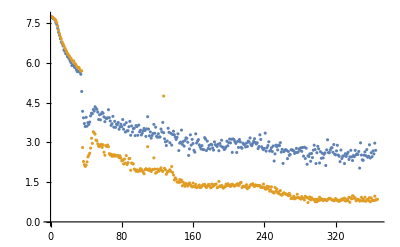

```mathematica
ListPlot[{train500data, test500data}]
```

```mathematica
trainordereddata = {7.779863421347122,7.749542774564768,7.714651527780529,7.692052583236482,7.649323421007664,7.610441690899095,7.542867932498519,7.472237458310072,7.388423141079072,7.309995546546928,7.22108987782725,7.1283852347007075,7.05426566519338,6.896766434474955,6.801920647743722,6.7526684691268555,6.6177041991255585,6.606898646111062,6.4844082638437435,6.419524993636525,6.329416104191885,6.2244010718464775,6.2026157783111895,6.196189301026015,6.124347412912721,6.03958603370506,5.999632513830285,5.886438428723593,5.771879845447691,4.283326969725578,4.406871577006918,4.200895978190921,4.201043826075175,4.127060398875626,3.7412488427627046,4.084229729285617,4.291072731833541,4.142518644951883,3.9682868553208293,3.945302923758905,3.8469179659070183,3.657064347278535,3.94692040592749,3.9739055779570185,3.8073522784572202,3.4662623723961716,3.785196890561873,3.6538182479166665,3.3621804474034995,3.329864965922638,3.5562648057076376,3.53195291680082,3.108681609572031,3.4262065266206103,3.3070522938331477,3.3534658436963274,3.3754619813202935,2.8522453207087386,3.35837113032564,3.382155684454898,3.0012563360304374,3.3383922104992183,3.564205163443114,3.3473978182450566,2.997017277936122,3.2110452879653364,3.31747396484079,3.08596499639354,3.1122217601689495,3.0572391915555075,2.7611476526661916,3.1746402808710443,3.2318381523405555,3.054857830103806,3.0837492693744664,3.3389229109933156,3.024996584385583,3.179058563850727,3.277351617881645,3.1229261809489426,2.772417070252672,2.9302078725207013,2.8768915470563026,3.0569001210167372,2.6263610438435285,2.9937007733971255,3.137458959301253,3.263666995418655,2.5085614128734517,2.8642819091619716,2.9448605870704427,3.1467490844042607,3.040000029015382,3.3014321631476595,3.116292070642296,2.956982184930674,3.0885892369937333,2.860236407850767,2.853739177135266,2.9670392366227425,3.3756959487212965,2.8411380221762546,3.367938467447376,2.95334509549586,3.0358830112614017,3.561232320463467,3.0447593223009766,2.8711109176448035,3.0480571858073233,2.8082541083103485,3.215964450348583,3.089900561270809,2.901984684612706,3.1855626151290624,3.037992442643597,3.2669876745970963,3.1240485589092946,2.9927153050674495,2.996453694485859,2.9962332807647765,2.7908033805222767,3.145961177009773,3.3501730388975277,2.9426245421143675,3.3256218362994923,3.0492084524715266,3.2262140971420594,3.2285023864722047,3.22975514331609,3.1760106517910462,3.381436012983024,3.1904086538536536,3.1571111596618686,3.0842890946567123,3.33554330434355,3.6103535416159347,3.168250582848135,3.674907566827053,3.132958118322963,3.2725079274486717,3.31264833825455,3.503613443204679,3.47417832245514,4.161321682189717,4.376122511810715,3.4688726592926873,3.566788995055168,3.4488874205840814,3.5227150601722945,3.618738981723119,3.553558483246357,3.345489485809588,3.607128703739333,3.557116134557798,3.251820568199236,3.2561510914981904,3.4225241886305238,3.4516681699292953,3.263555737348049,3.268747862323072,3.5903603217231854,3.47187236755605,3.462669621885942,3.528882306759649,3.448903610384087,3.4711462437840397,3.4135719866912364,3.615904327938581,3.3687998029292965,3.4251578723970755,3.10840782756925,3.3084057139735195,3.660777922214671,3.632217827758751,3.4407280091175347,3.4409942259037027,3.529511107711586,3.6296328714697,3.521720724732193,3.443732575219567,3.522682347681618,3.5771268011267847,3.336871602663132,3.5166056839554316,3.378556598972971,3.5844702067913006,3.3983139606005532,3.3682895703715694,3.4838830084794887,3.7355061314221816,3.5516989702271804,3.7410403218365103,3.7409414450590224,3.5694324177549857,3.483383876818097,3.6871505350082376,3.670294620657472,3.4963081190771264,3.6404774108892415,3.7945960870692876,3.493518467126809,3.6604797731001804,3.6659788988130937,3.462507809373175,3.5564701150678677,3.477720435404626,3.5217346580381643,3.313870348576563,3.390706360166123,3.550506776787748,3.634064522621537,3.3655980864717363,3.8220148636287785,3.626855918067899,3.6992032833381425,3.3373279616751512,3.617522682995946,3.4474513680504786,3.626139976459904,3.8386593797478463,3.547472578228756,3.5056078101380983,3.7551150897541477,3.627970953007258,3.4992564940166626,3.6618683344750593,3.521206467290872,3.8379348266703386,3.7978331658552675,3.814723737846886,3.898815667860647,3.8420727959914642,3.6788719448791567,3.3473436256316784,3.4315248374945693,3.5775182436816366,3.8053619581612823,3.6849337800412147,3.6352045829564257,3.6448770256542384,3.520251947987687,3.73592377243486,3.6142114272902433,3.8840286041033854,3.8477003377577255,3.983254812721952,3.836476688353689,3.9693912277800636,3.7679055016565473,3.681872954133396,3.664284500784476,3.880191225354324,4.0036809131793145,4.1429490442507095,4.166853806229364,4.183528652572236,3.9674882550733543,4.02868486761341,3.9250706126509765,3.918382778446656,4.076532566960293,4.057867867137949,4.027415192044545,3.9625019503798176,3.9509225833874195,4.1522292210596365,4.023536046479748,4.276926866769202,4.144989367485235,4.079616816711381,4.226608307354219,4.180782941767348,4.360910670049453,4.307634269509664,4.2869397054931335,4.367768121631048,4.343892949360477,4.156291940480209,4.367993960038776,4.203085285240163,4.215957335756005,4.254977981743063,4.279048506363528,4.357503123292368,4.320018497809958,4.3117566643891845,4.39062896699302,4.305444602355859,4.3292870764598765,4.1902209195492235,4.1091860521481065,4.3633369427416895,4.23835872929993,4.305102740191192,4.14094684706541,4.171759534759011,4.2888083510328,4.4984497076482155,4.303927234606237,4.292752941483184,4.313802911041445,4.402081511921736,4.134646818303386,4.191807773940214,4.3068028854691915,4.210113770679004,4.294638979439112,4.380652892438706,4.417493900189374,4.200181857580847,4.3001421537044,4.476150983284635,4.2657377477879015,4.310839472057063,4.1852181051807085,4.270689972964043,4.23685470683089,4.34912699737993,4.098581250910372,4.376553439149271,4.114564391111665,4.3881100869687835,4.226255275793141,4.462953445232011,4.184622210911369,4.168665152138068,4.197507505259164,4.190762282120823,4.20451055565401,4.328997109579974,4.415641683646498,4.108096571310912,4.31814499965602,4.162364321110961,4.278760126021129,4.0929040413235205,4.172444138225439,4.08430862936522,4.121900486941985,4.343367534483987,4.291977969543427,4.239638336237458,4.303182504932442,4.481552218681877,4.443083889779243,4.213061216057453,4.23456361033726,4.097411789329956,4.269817949440142,4.237508352898988,4.259986610961362,4.251789094757802,4.3753862313961625,4.330291852076552,4.261073816359908,4.352933472388548,4.483117393720583,4.368127033756703,4.132286052095553,4.17565796088235,4.026503342953236,4.279723169315258,4.3915834999002445,4.301483475925629,4.266482858269261,4.105422552855825,4.302347341277662,4.2448548120746565,4.058179146669199,4.1884550141157675,4.251333092221745,4.346045462833006,4.008395660909333,4.206601054660414,4.274154716543233,4.208003511908038,4.317552844800287,4.266101458500413,4.315452798423099,4.134440716455756,4.298410027037085,4.173001480102088,4.351899589452838}
```

{7.77986,7.74954,7.71465,7.69205,7.64932,7.61044,7.54287,7.47224,7.38842,7.31,7.22109,7.12839,7.05427,6.89677,6.80192,6.75267,6.6177,6.6069,6.48441,6.41952,6.32942,6.2244,6.20262,6.19619,6.12435,6.03959,5.99963,5.88644,5.77188,4.28333,4.40687,4.2009,4.20104,4.12706,3.74125,4.08423,4.29107,4.14252,3.96829,3.9453,3.84692,3.65706,3.94692,3.97391,3.80735,3.46626,3.7852,3.65382,3.36218,3.32986,3.55626,3.53195,3.10868,3.42621,3.30705,3.35347,3.37546,2.85225,3.35837,3.38216,3.00126,3.33839,3.56421,3.3474,2.99702,3.21105,3.31747,3.08596,3.11222,3.05724,2.76115,3.17464,3.23184,3.05486,3.08375,3.33892,3.025,3.17906,3.27735,3.12293,2.77242,2.93021,2.87689,3.0569,2.62636,2.9937,3.13746,3.26367,2.50856,2.86428,2.94486,3.14675,3.04,3.30143,3.11629,2.95698,3.08859,2.86024,2.85374,2.96704,3.3757,2.84114,3.36794,2.95335,3.03588,3.56123,3.04476,2.87111,3.04806,2.80825,3.21596,3.0899,2.90198,3.18556,3.03799,3.26699,3.12405,2.99272,2.99645,2.99623,2.7908,3.14596,3.35017,2.94262,3.32562,3.04921,3.22621,3.2285,3.22976,3.17601,3.38144,3.19041,3.15711,3.08429,3.33554,3.61035,3.16825,3.67491,3.13296,3.27251,3.31265,3.50361,3.47418,4.16132,4.37612,3.46887,3.56679,3.44889,3.52272,3.61874,3.55356,3.34549,3.60713,3.55712,3.25182,3.25615,3.42252,3.45167,3.26356,3.26875,3.59036,3.47187,3.46267,3.52888,3.4489,3.47115,3.41357,3.6159,3.3688,3.42516,3.10841,3.30841,3.66078,3.63222,3.44073,3.44099,3.52951,3.62963,3.52172,3.44373,3.52268,3.57713,3.33687,3.51661,3.37856,3.58447,3.39831,3.36829,3.48388,3.73551,3.5517,3.74104,3.74094,3.56943,3.48338,3.68715,3.67029,3.49631,3.64048,3.7946,3.49352,3.66048,3.66598,3.46251,3.55647,3.47772,3.52173,3.31387,3.39071,3.55051,3.63406,3.3656,3.82201,3.62686,3.6992,3.33733,3.61752,3.44745,3.62614,3.83866,3.54747,3.50561,3.75512,3.62797,3.49926,3.66187,3.52121,3.83793,3.79783,3.81472,3.89882,3.84207,3.67887,3.34734,3.43152,3.57752,3.80536,3.68493,3.6352,3.64488,3.52025,3.73592,3.61421,3.88403,3.8477,3.98325,3.83648,3.96939,3.76791,3.68187,3.66428,3.88019,4.00368,4.14295,4.16685,4.18353,3.96749,4.02868,3.92507,3.91838,4.07653,4.05787,4.02742,3.9625,3.95092,4.15223,4.02354,4.27693,4.14499,4.07962,4.22661,4.18078,4.36091,4.30763,4.28694,4.36777,4.34389,4.15629,4.36799,4.20309,4.21596,4.25498,4.27905,4.3575,4.32002,4.31176,4.39063,4.30544,4.32929,4.19022,4.10919,4.36334,4.23836,4.3051,4.14095,4.17176,4.28881,4.49845,4.30393,4.29275,4.3138,4.40208,4.13465,4.19181,4.3068,4.21011,4.29464,4.38065,4.41749,4.20018,4.30014,4.47615,4.26574,4.31084,4.18522,4.27069,4.23685,4.34913,4.09858,4.37655,4.11456,4.38811,4.22626,4.46295,4.18462,4.16867,4.19751,4.19076,4.20451,4.329,4.41564,4.1081,4.31814,4.16236,4.27876,4.0929,4.17244,4.08431,4.1219,4.34337,4.29198,4.23964,4.30318,4.48155,4.44308,4.21306,4.23456,4.09741,4.26982,4.23751,4.25999,4.25179,4.37539,4.33029,4.26107,4.35293,4.48312,4.36813,4.13229,4.17566,4.0265,4.27972,4.39158,4.30148,4.26648,4.10542,4.30235,4.24485,4.05818,4.18846,4.25133,4.34605,4.0084,4.2066,4.27415,4.208,4.31755,4.2661,4.31545,4.13444,4.29841,4.173,4.3519}

```mathematica
testordereddata = {7.795415878295898,7.76535701751709,7.739620685577393,7.7125043869018555,7.679856300354004,7.64383602142334,7.592750072479248,7.526163578033447,7.4441022872924805,7.368820667266846,7.292525768280029,7.21237850189209,7.127078056335449,7.03856086730957,6.9507269859313965,6.866624355316162,6.784297943115234,6.705328464508057,6.628381252288818,6.558205604553223,6.489936828613281,6.4245829582214355,6.360955715179443,6.301911354064941,6.246558666229248,6.191822528839111,6.140106678009033,6.0906219482421875,6.0418524742126465,3.2752628326416016,2.9064645767211914,2.74135160446167,2.7335052490234375,2.7401363849639893,2.746096134185791,2.7236695289611816,2.7168781757354736,2.6250901222229004,2.5064101219177246,2.4614956378936768,2.426614761352539,2.322625160217285,2.267418146133423,2.2248547077178955,2.1489474773406982,2.079962968826294,2.032219648361206,2.026826858520508,2.0018696784973145,1.997536540031433,1.9874464273452759,1.9432616233825684,1.9146312475204468,1.8982723951339722,1.8788975477218628,1.7931420803070068,1.790664792060852,1.7553383111953735,1.7469804286956787,1.6804536581039429,1.6429311037063599,1.6120800971984863,1.5481648445129395,1.5367581844329834,1.489318609237671,1.5266568660736084,1.4837627410888672,1.4655373096466064,1.4372344017028809,1.435925006866455,1.4222944974899292,1.4083857536315918,1.3926031589508057,1.378144383430481,1.35955011844635,1.3544495105743408,1.3465145826339722,1.3346216678619385,1.3216536045074463,1.3141255378723145,1.310543417930603,1.308008074760437,1.3060880899429321,1.3041244745254517,1.302388072013855,1.3004173040390015,1.2984975576400757,1.2970317602157593,1.2957931756973267,1.2939457893371582,1.292515516281128,1.291090726852417,1.2899954319000244,1.2885944843292236,1.2876362800598145,1.2863012552261353,1.285057544708252,1.2841708660125732,1.2883259057998657,1.2890279293060303,1.3122225999832153,1.311318278312683,1.30605149269104,1.3227628469467163,1.2957251071929932,1.2906835079193115,1.2872861623764038,1.298478364944458,1.3121676445007324,1.3244493007659912,1.3284645080566406,1.3280644416809082,1.3560823202133179,1.362619161605835,1.3550024032592773,1.3727914094924927,1.4142173528671265,1.4343358278274536,1.4579989910125732,1.5025132894515991,1.4738572835922241,1.5208361148834229,1.556962013244629,1.6995612382888794,1.924268364906311,2.0089054107666016,1.9268760681152344,1.8539127111434937,1.9204596281051636,1.8940092325210571,2.0760340690612793,2.3744890689849854,2.577383279800415,2.0596320629119873,2.0006160736083984,2.0501813888549805,2.015141010284424,2.0071749687194824,2.2075858116149902,2.145714044570923,2.152775764465332,2.171055793762207,2.1385178565979004,2.9044301509857178,4.088445663452148,2.848323345184326,2.6790730953216553,2.6369123458862305,2.6133506298065186,2.4014317989349365,2.2577877044677734,2.388415813446045,2.4857184886932373,2.440131902694702,2.488680362701416,2.4989094734191895,2.581836462020874,2.645369291305542,2.5573809146881104,2.518768787384033,2.6598432064056396,2.5129854679107666,2.65657639503479,2.5148441791534424,2.495790481567383,2.6643567085266113,2.9744961261749268,2.8995347023010254,2.5427238941192627,2.5124590396881104,2.5510575771331787,2.599612236022949,2.740523338317871,2.8438737392425537,2.991450309753418,2.7686729431152344,2.908665657043457,2.984354019165039,2.7847306728363037,2.771462917327881,2.773686170578003,2.886521577835083,2.728297472000122,2.6540110111236572,2.7551207542419434,2.7138402462005615,2.6640899181365967,2.7234182357788086,2.802093267440796,2.9374284744262695,3.029893636703491,3.0640981197357178,3.0278706550598145,2.9204912185668945,2.8061141967773438,2.8098251819610596,2.8405613899230957,2.8226475715637207,2.8083558082580566,2.8302841186523438,2.796029567718506,2.905888080596924,2.8762869834899902,2.8415136337280273,2.8134615421295166,2.820216655731201,2.8352177143096924,2.8191967010498047,2.8157591819763184,2.8677780628204346,2.8912994861602783,2.86607027053833,2.953228712081909,3.037684440612793,3.0160305500030518,2.9760024547576904,3.0619730949401855,3.0404458045959473,3.0342135429382324,3.0647552013397217,3.1249895095825195,3.0837481021881104,3.117175579071045,3.130657196044922,3.178081750869751,3.192117929458618,3.166388988494873,3.1893231868743896,3.2974305152893066,3.3217363357543945,3.334102153778076,3.3310024738311768,3.2300474643707275,3.1949918270111084,3.2244479656219482,3.2626264095306396,3.3049721717834473,3.276272773742676,3.393441677093506,3.37937331199646,3.325936794281006,3.4024956226348877,3.4763593673706055,3.467921733856201,3.692540168762207,3.801929473876953,3.8037962913513184,3.843806505203247,3.7856080532073975,3.791977882385254,3.911532402038574,3.85684871673584,3.980799913406372,4.081905364990234,4.0992608070373535,4.181085109710693,4.171923637390137,4.219372749328613,4.131218910217285,4.10463809967041,4.235159397125244,4.269457817077637,4.3197784423828125,4.296750545501709,4.327297687530518,4.339230060577393,4.522063255310059,4.72519063949585,4.7879414558410645,4.640412330627441,4.7404890060424805,4.826693534851074,4.731576919555664,4.888873100280762,4.899868488311768,4.967851638793945,4.949733734130859,4.980100154876709,5.0579729080200195,5.089991569519043,4.933882713317871,4.999186038970947,5.114124298095703,5.162168025970459,5.099993705749512,5.169924736022949,5.15086555480957,5.138628005981445,5.055363655090332,5.201437950134277,5.066395282745361,5.083282470703125,5.1345930099487305,5.114882946014404,5.231318950653076,5.20724630355835,5.099065780639648,5.245704650878906,5.173933506011963,5.171776294708252,5.153457164764404,5.168858528137207,5.1890645027160645,5.200919151306152,5.2274346351623535,5.208333969116211,5.230770111083984,5.297191143035889,5.248525142669678,5.253221035003662,5.207015514373779,5.197187900543213,5.25010871887207,5.202175140380859,5.2247700691223145,5.270987510681152,5.231919765472412,5.222012519836426,5.216658115386963,5.266550540924072,5.2580084800720215,5.276345252990723,5.25837516784668,5.28461217880249,5.242861270904541,5.24660062789917,5.265156269073486,5.252090930938721,5.2388811111450195,5.267185211181641,5.255519866943359,5.260039806365967,5.289346218109131,5.2436137199401855,5.256080150604248,5.2487473487854,5.253922462463379,5.264936923980713,5.26472282409668,5.294830322265625,5.261597633361816,5.253703594207764,5.304574966430664,5.290823936462402,5.297152042388916,5.322481155395508,5.306005001068115,5.286901950836182,5.291693687438965,5.28877067565918,5.310597896575928,5.318021774291992,5.30076265335083,5.308177947998047,5.301019668579102,5.299357891082764,5.307096004486084,5.320119857788086,5.307867050170898,5.302345275878906,5.309268474578857,5.289384365081787,5.282412528991699,5.319773197174072,5.3050432205200195,5.326614856719971,5.311168193817139,5.319894790649414,5.291985034942627,5.305386543273926,5.317739963531494,5.3433332443237305,5.345354080200195,5.290207862854004,5.318940162658691,5.3268842697143555,5.387317657470703,5.319824695587158,5.356897830963135,5.368983268737793,5.35368013381958,5.3443827629089355,5.345929145812988,5.342404842376709,5.342400550842285}
```

{7.79542,7.76536,7.73962,7.7125,7.67986,7.64384,7.59275,7.52616,7.4441,7.36882,7.29253,7.21238,7.12708,7.03856,6.95073,6.86662,6.7843,6.70533,6.62838,6.55821,6.48994,6.42458,6.36096,6.30191,6.24656,6.19182,6.14011,6.09062,6.04185,3.27526,2.90646,2.74135,2.73351,2.74014,2.7461,2.72367,2.71688,2.62509,2.50641,2.4615,2.42661,2.32263,2.26742,2.22485,2.14895,2.07996,2.03222,2.02683,2.00187,1.99754,1.98745,1.94326,1.91463,1.89827,1.8789,1.79314,1.79066,1.75534,1.74698,1.68045,1.64293,1.61208,1.54816,1.53676,1.48932,1.52666,1.48376,1.46554,1.43723,1.43593,1.42229,1.40839,1.3926,1.37814,1.35955,1.35445,1.34651,1.33462,1.32165,1.31413,1.31054,1.30801,1.30609,1.30412,1.30239,1.30042,1.2985,1.29703,1.29579,1.29395,1.29252,1.29109,1.29,1.28859,1.28764,1.2863,1.28506,1.28417,1.28833,1.28903,1.31222,1.31132,1.30605,1.32276,1.29573,1.29068,1.28729,1.29848,1.31217,1.32445,1.32846,1.32806,1.35608,1.36262,1.355,1.37279,1.41422,1.43434,1.458,1.50251,1.47386,1.52084,1.55696,1.69956,1.92427,2.00891,1.92688,1.85391,1.92046,1.89401,2.07603,2.37449,2.57738,2.05963,2.00062,2.05018,2.01514,2.00717,2.20759,2.14571,2.15278,2.17106,2.13852,2.90443,4.08845,2.84832,2.67907,2.63691,2.61335,2.40143,2.25779,2.38842,2.48572,2.44013,2.48868,2.49891,2.58184,2.64537,2.55738,2.51877,2.65984,2.51299,2.65658,2.51484,2.49579,2.66436,2.9745,2.89953,2.54272,2.51246,2.55106,2.59961,2.74052,2.84387,2.99145,2.76867,2.90867,2.98435,2.78473,2.77146,2.77369,2.88652,2.7283,2.65401,2.75512,2.71384,2.66409,2.72342,2.80209,2.93743,3.02989,3.0641,3.02787,2.92049,2.80611,2.80983,2.84056,2.82265,2.80836,2.83028,2.79603,2.90589,2.87629,2.84151,2.81346,2.82022,2.83522,2.8192,2.81576,2.86778,2.8913,2.86607,2.95323,3.03768,3.01603,2.976,3.06197,3.04045,3.03421,3.06476,3.12499,3.08375,3.11718,3.13066,3.17808,3.19212,3.16639,3.18932,3.29743,3.32174,3.3341,3.331,3.23005,3.19499,3.22445,3.26263,3.30497,3.27627,3.39344,3.37937,3.32594,3.4025,3.47636,3.46792,3.69254,3.80193,3.8038,3.84381,3.78561,3.79198,3.91153,3.85685,3.9808,4.08191,4.09926,4.18109,4.17192,4.21937,4.13122,4.10464,4.23516,4.26946,4.31978,4.29675,4.3273,4.33923,4.52206,4.72519,4.78794,4.64041,4.74049,4.82669,4.73158,4.88887,4.89987,4.96785,4.94973,4.9801,5.05797,5.08999,4.93388,4.99919,5.11412,5.16217,5.09999,5.16992,5.15087,5.13863,5.05536,5.20144,5.0664,5.08328,5.13459,5.11488,5.23132,5.20725,5.09907,5.2457,5.17393,5.17178,5.15346,5.16886,5.18906,5.20092,5.22743,5.20833,5.23077,5.29719,5.24853,5.25322,5.20702,5.19719,5.25011,5.20218,5.22477,5.27099,5.23192,5.22201,5.21666,5.26655,5.25801,5.27635,5.25838,5.28461,5.24286,5.2466,5.26516,5.25209,5.23888,5.26719,5.25552,5.26004,5.28935,5.24361,5.25608,5.24875,5.25392,5.26494,5.26472,5.29483,5.2616,5.2537,5.30457,5.29082,5.29715,5.32248,5.30601,5.2869,5.29169,5.28877,5.3106,5.31802,5.30076,5.30818,5.30102,5.29936,5.3071,5.32012,5.30787,5.30235,5.30927,5.28938,5.28241,5.31977,5.30504,5.32661,5.31117,5.31989,5.29199,5.30539,5.31774,5.34333,5.34535,5.29021,5.31894,5.32688,5.38732,5.31982,5.3569,5.36898,5.35368,5.34438,5.34593,5.3424,5.3424}

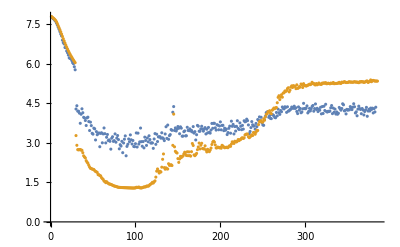

```mathematica
ListPlot[{trainordereddata, testordereddata}]
```